```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Thu 1 Jun 2023 09:38:15

13.2.0 for Microsoft Windows (64-bit) (November 18, 2022)

6.0.2 (June 28, 2021)

## Lecture 18 edited by Chi-Ok Hwang, originally made by Prof. 정 영주

[1] C. Arangala, Exploring Linear Algebra: Labs and Projects with Mathematica ®, 1st ed. Boca Raton: Chapman and Hall/CRC, 2014.

-Graphics-

$UserBaseDirectory
gives the base directory in which user-specific files to be loaded by the Wolfram System are conventionally placed.

How to change the default Mathematica environments!
Make your own Default.nb and put it in the following directory!
C:\Users\admin\AppData\Roaming\Mathematica\SystemFiles\FrontEnd\StyleSheets

## First-Order Ordinary Differential Equations (ODEs)

### Direction Fields

The general form of first-order ODE is

y'=ⅆy/ⅆx=(g(x,y))/(f(x,y))

Then the direction field is the 2-D vector function (f(x,y),g(x,y)), which specifies the direction of the solution curve in the xy-plane.

Consider the ODE

y'=ⅆy/ⅆx=y+x

The direction field is (1,y+x).

The solution is

SCDSolve[{("eqn")_1, ("eqn")_2, …}, {("y")_1, ("y")_2, …}, x] solves a set of differential equations with independent variable x.
SCDSolve[eqn, y, {("x")_1, ("x")_2, …}] solves the partial differential equation eqn.

```mathematica
y'==y+x
SCMAF[%,SCDSolve,{All,y[0]==Subscript[y, 0],y[x],x},Hold-> Subscript[y, 0]]
```

y'==x+y

y[x]==-1+ⅇ^x-x+ⅇ^x y_0

Plot of the direction field and the solution curves passing through different points (0,y_0)

StreamPlotpaclet:ref/StreamPlot[{v_x,v_y},{x,x_min,x_max},{y,y_min,y_max}] 
generates a stream plot of the vector field {v_x,v_y} as a function of x and y.

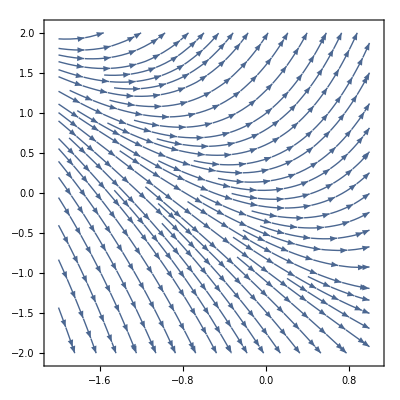

```mathematica
StreamPlot[{1,y+x},{x,-2,1},{y,-2,2}]
```

0

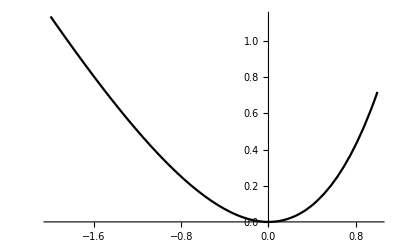

```mathematica
y0 =  0
Plot[-1+ⅇ^x-x+ⅇ^x y0,{x,-2,1},PlotStyle->Black]
```

```mathematica
Manipulate[
Show[StreamPlot[{1,y+x},{x,-2,1},{y,-2,2},Axes->True,Frame->False,AxesLabel->{x,y}],
Plot[-1+ⅇ^x-x+ⅇ^x y0,{x,-2,1},PlotStyle->Black],
Graphics[{PointSize[0.03],Point[{0,y0}]}]],
{{y0,0,Subscript[y, 0]},Range[-2,2]}]
```

```mathematica
DSolve
```

### Separable Equations

Separate the variables

y'=F(x,y)    ⟶    f(x)ⅆx=g(y)ⅆy    ⟶    ∫f(x)ⅆx=∫g(y)ⅆy

The most general separable equation (first order) is

y'(x)=a(x)b(y)

Direct integration gives the general solution

```mathematica
y'[x]==a[x]b[y]
SCMAF[%,SCAbbrevDeriv,At[1],,
SCSepVars,{All,y},
SCDiffToInt,All,Plus->{At[2],c}]
```

y'[x]==a[x] b[y]

ⅆy/ⅆx==a[x] b[y]

ⅆy/b[y]==a[x] ⅆx

∫1/b[y]ⅆy==c+∫a[x]ⅆx

◼ SCSepVars[expr, vars] separates factors by putting the variables vars on the same side (left by default).
◼ SCSepVars[expr, vars, op] separates factors by putting the variables vars on the same side (left by default) using the operator op.

```mathematica
SCSepVars[ⅆy/ⅆx==2 ⅇ^(x-y)y,x]
```

ⅇ^x ⅆx==(ⅇ^y ⅆy)/(2 y)

◼ SCAbbrevDerivPrime[expr] abbreviates the primed derivatives to total or partial derivatives.
◼ SCAbbrevDerivPrime[expr, var] abbreviates the primed derivatives to total or partial derivatives with var as the independent variable.

```mathematica
SCAbbrevDerivPrime[f',x]
```

ⅆf/ⅆx

◼ SCDiffToInt[expr] transforms differentials to integral form.
◼ SCDiffToInt[expr, vars_1, vars_2, …] transforms differentials to integral form for the variables vars_i.

```mathematica
SCDiffToInt[ⅆv/v+ⅆx/x==0,x,v,Constant->c]
```

∫1/v ⅆv+∫1/x ⅆx==c

◼ SCEqMap[eq, f] applies the function f to all terms of the equation eq.

```mathematica
SCEqMap[a==b+c,F,Distribute->True]
```

F[a]==F[b]+F[c]

Example: y'=x ⅇ^-x(1+y^2)

```mathematica
y'==x ⅇ^-x(1+y^2)
SCMAF[%,SCAbbrevDerivPrime,{At[1],x},
SCSepVars,{All,y},
SCDiffToInt,All,
SCEvalInt,All,Plus->{At[2],c},ChangeSign->-1-x,
SCEqMap,{All,Tan}]
```

y'==ⅇ^-x x (1+y^2)

ArcTan[y]==c-ⅇ^-x (1+x)

y==Tan[c-ⅇ^-x (1+x)]

Direct solution using DSolve

```mathematica
y'==x ⅇ^-x(1+y^2)
SCMAF[%,SCDSolve,{All,y,x,ReplConst->c,Post->{Factor,-ⅇ^-x-ⅇ^-x x,ExpandAll}}]
```

y'==ⅇ^-x x (1+y^2)

y==Tan[c-ⅇ^-x (1+x)]

### Exact ODEs and Integrating Factors

Another general form of the first-order differential equation is

M(x,y)ⅆx+N(x,y)ⅆy=0.

Example: The first-order ODE

ⅆy/ⅆx=(x-3y)/(2y-x)

can be put in the form

```mathematica
ⅆy/ⅆx==(x-3y)/(2y-x)
SCMAF[%,SCEqCrossMult,All,
SCEqMerge,{All,Right},ChangeSign->-x+2 y]
```

ⅆy/ⅆx==(x-3 y)/(-x+2 y)

(-x+2 y) ⅆy==(x-3 y) ⅆx

(SCEqMerge $)[-(x-2 y) ⅆy==(x-3 y) ⅆx,Right]

so that

M(x,y)=x-3y,    N(x,y)=x-2y·

The condition for the equation to be exact is

(∂M)/(∂y)=(∂N)/(∂x)·

For the above equation

```mathematica
SCARA[(∂M)/(∂y)==(∂N)/(∂x),{M==x-3y,N==x-2y},Post->SCEvalDeriv]
```

((∂M)/(∂y)==(∂N)/(∂x))==False

and therefore, the equation is not exact. However, for the equation

cos(x+y)ⅆx+(3 y^2+2y+cos(x+y))ⅆy=0,

```mathematica
SCARA[(∂M)/(∂y)==(∂N)/(∂x),{M==Cos[x+y],N==3 y^2+2y+Cos[x+y]},Post->SCEvalDeriv]
```

((∂M)/(∂y)==(∂N)/(∂x))==True

and the equation is exact. If the solution is sought in the form u(x,y)=c, since

```mathematica
ⅆu[x,y]==0
SCMAF[%,SCDerivExpand,At[1],Post->SCAbbrevFunc]
```

ⅆu[x,y]==0

ⅆx (∂u)/(∂x)+ⅆy (∂u)/(∂y)==0

we have

M=(∂u)/(∂x)=cos(x+y),    N=(∂u)/(∂y)=3 y^2+2y+cos(x+y).

The solution is then

```mathematica
u==∫Mⅆx+f[y]
SCMAF[%,RA,{At[2],M==Cos[x+y]},
SCEvalInt,At[2],Post->TrigReduce]
```

u==f[y]+∫Mⅆx

u==f[y]+∫Cos[x+y]ⅆx

u==f[y]+Sin[x+y]

where f(y) is an arbitrary function of y. The second equation then gives

```mathematica
(∂u)/(∂y)==3 y^2+2y+Cos[x+y]
SCMAF[%,RA,{All,u==f[y]+Sin[x+y]},Post->{SCSolve->f'[y],SCEvalDeriv},
SCDSolve,{All,f[y],y,ReplConst->0}]
```

(∂u)/(∂y)==2 y+3 y^2+Cos[x+y]

f'[y]==2 y+3 y^2

f[y]==y^2+y^3

and therefore, the solution is

```mathematica
u==c
SCMAF[%,RR,{At[1],{u[x,y]==f[y]+Sin[x+y],f[y]==y^2+y^3}}]
```

u[x,y]==c

y^2+y^3+Sin[x+y]==c

Alternatively, using SCDerivSimp,

```mathematica
Cos[x+y]ⅆx+(3 y^2+2y+Cos[x+y])ⅆy==0
SCMAF[%,SCDerivSimp,At[1]]
```

Cos[x+y] ⅆx+(2 y+3 y^2+Cos[x+y]) ⅆy==0

ⅆ(y^2+y^3+Sin[x+y])==0

Contour plot of the solution with c as the parameter

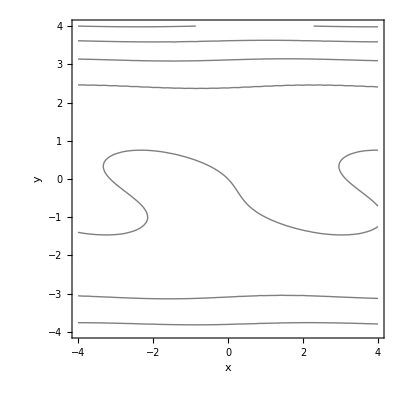

```mathematica
ContourPlot[y^2+y^3+Sin[x+y],{x,-4,4},{y,-4,4},FrameLabel->{"x","y"},ContourShading->False]
```

Inexact ODEs can be made exact by multiplying μ to M and N, respectively:

M(x,y)ⅆx+N(x,y)ⅆy=0    ⟶    μ M(x,y)ⅆx+μ N(x,y)ⅆy=0.

where the integrating factor μ satisfies the equation

(∂(μ M))/(∂y)=(∂(μ N))/(∂x).

Example: The equation -yⅆx+xⅆy=0 is not exact because M=-y,N=x, and

```mathematica
SCARA[{(∂M)/(∂y),(∂N)/(∂x)},{M==-y,N==x},PostAll->Thread]
```

{(∂M)/(∂y)==-1,(∂N)/(∂x)==1}

and thus (∂M)/(∂y)≠(∂N)/(∂x). Let us show that in such a case the present method does not work. The solution is

```mathematica
u==∫Mⅆx+k[y]
SCMAF[%,RA,{At[2],M==-y},Post->SCEvalInt]
```

u==k[y]+∫Mⅆx

u==-x y+k[y]

hence

```mathematica
(∂u)/(∂y)==N
SCMAF[%,RA,{All,{u==-x y+k[y],N==x}},Post->SCEvalDeriv,
SCEqMove,{All,k'[y]}]
```

(∂u)/(∂y)==N

-x+k'[y]==x

k'[y]==2 x

This equation cannot hold since k(y) depends only on y. Using separation of variables, the solution is obtained as:

```mathematica
-yⅆx+xⅆy==0
SCMAF[%,SCEqMove,{All,xⅆy},SCSepVars-> y,
SCDiffToInt,All,Plus->{At[2],Log[c]},
SCEvalInt,All,SCEqMap->Exp]
```

-y ⅆx+x ⅆy==0

∫1/y ⅆy==Log[c]+∫1/x ⅆx

y==c x

Assuming that the integrating factor μ is a function of x only (μ=μ(x)), we have

```mathematica
(∂(μ M))/(∂y)==(∂(μ N))/(∂x)
SCMAF[%,RA,{All,{μ==μ[x],M==-y,N==x}},Post->SCEvalDeriv,
SCSolve,{All,μ'[x]},
SCDSolve,{All,μ[x],x,ReplConst->1}]
```

(∂(M μ))/(∂y)==(∂(N μ))/(∂x)

μ'[x]==-(2 μ[x])/x

μ[x]==1/x^2

The solution is then

```mathematica
u==∫μ Mⅆx+k[y]
SCMAF[%,RA,{At[2],{μ==1/x^2,M==-y}},Post->SCEvalInt]
```

u==k[y]+∫M μⅆx

u==y/x+k[y]

hence

```mathematica
(∂u)/(∂y)==μ N
SCMAF[%,RA,{All,{u==y/x+k[y],μ==1/x^2,N==x}},Post->SCEvalDeriv,
SCEqMove,{All,k'[y]}]
```

(∂u)/(∂y)==N μ

1/x+k'[y]==1/x

k'[y]==0

We set k(y)=0, and the solution is y/x=c or y=c x.

Alternatively, assuming that the integrating factor μ is a function of y only (μ=μ(y)), we have

```mathematica
(∂(μ M))/(∂y)==(∂(μ N))/(∂x)
SCMAF[%,RA,{All,{μ==μ[y],M==-y,N==x}},Post->SCEvalDeriv,
SCSolve,{All,μ'[y]},
SCDSolve,{All,μ[y],y,ReplConst->1}]
```

(∂(M μ))/(∂y)==(∂(N μ))/(∂x)

μ'[y]==-(2 μ[y])/y

μ[y]==1/y^2

The solution is then

```mathematica
u==∫μ Mⅆx+k[y]
SCMAF[%,RA,{At[2],{μ==1/y^2,M==-y}},Post->SCEvalInt]
```

u==k[y]+∫M μⅆx

u==-x/y+k[y]

hence

```mathematica
(∂u)/(∂y)==μ N
SCMAF[%,RA,{All,{u==-x/y+k[y],μ==1/y^2,N==x}},Post->SCEvalDeriv,
SCEqMove,{All,k'[y]}]
```

(∂u)/(∂y)==N μ

x/y^2+k'[y]==x/y^2

k'[y]==0

We set k(y)=0, and the solution is -x/y=c or y=-x/c.

Other integrating factors are also possible:

```mathematica
SCDerivIntFactor[-yⅆx+xⅆy]
```

{1/x^2,1/y^2,1/(x y),1/(x+y)^2,1/(x-y)^2,1/(x^2+y^2),1/(x^2-y^2)}

which correspond to

```mathematica
SCDerivSimp[-yⅆx+xⅆy,Part->All,Post->SCMergeLogs]
```

{x^2 ⅆ y/x,-y^2 ⅆ x/y,x y ⅆLog[y/x],(x+y)^2 ⅆ y/(x+y),(x-y)^2 ⅆ y/(x-y),-(x^2+y^2) ⅆArcTan[x/y],(x^2-y^2) ⅆArcTanh[x/y]}

All of these give the equivalent solution y/x=c.

### Linear First-Order ODEs

The general form of the linear first-order ODEs

ⅆy/ⅆx+P(x)y=Q(x).

Direct solution using DSolve:

```mathematica
ⅆy/ⅆx+P[x]y==Q[x]
SCMAF[%,SCDSolve,{All,y,x,ReplVar->{x',x''},Limit->Null,ReplConst->c},
SCFactor,{At[2],ⅇ^(-∫^x P[x']ⅆ x')}]
```

y P[x]+ⅆy/ⅆx==Q[x]

y==c ⅇ^(-∫^x P[x']ⅆ x')+ⅇ^(-∫^x P[x']ⅆ x') ∫^x ⅇ^(∫^x'' P[x']ⅆ x') Q[x'']ⅆ x''

y==ⅇ^(-∫^x P[x']ⅆ x') (c+∫^x ⅇ^(∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')

Derivation of the formula. The equation can be put in the form

```mathematica
ⅆy/ⅆx+P[x]y==Q[x]
SCMAF[%,SCEqMove,{All,ⅆy/ⅆx},
SCEqCrossMult,All,Post->{Expand,SCEqMerge},Collect->{At[1],ⅆx}]
```

y P[x]+ⅆy/ⅆx==Q[x]

ⅆy/ⅆx==-y P[x]+Q[x]

ⅆy+ⅆx (y P[x]-Q[x])==0

Assuming the integrating factor is a function of x, i.e. μ=μ(x), the condition for the exact equation gives

```mathematica
(∂(μ M))/(∂y)==(∂(μ N))/(∂x)
SCMAF[%,RA,{All,{M==y P[x]-Q[x],N==1,μ==μ[x]}},Post->SCEvalDeriv,
SCDSolve,{All,μ[x],x,ReplConst->1,ReplVar->x',Limit->Null}]
```

(∂(M μ))/(∂y)==(∂(N μ))/(∂x)

P[x] μ[x]==μ'[x]

μ[x]==ⅇ^(∫^x P[x']ⅆ x')

Multiply the integrating factor, rearrange the terms and obtain the solution y.

```mathematica
ⅆy+ⅆx (y P[x]-Q[x])==0
SCMAF[%,Expand,At[1],
SCMoveTerm,{All,ⅆx Q[x]},
SCMultEq,{All,ⅇ^(∫^x P[x']ⅆ x')},Post->Expand,
RA,{All,ⅇ^(∫^x P[x']ⅆ x') ⅆy+ⅇ^(∫^x P[x']ⅆ x') y ⅆx P[x]==ⅆ(y ⅇ^(∫^x P[x']ⅆ x'))},SCDiffToInt->Constant->c,
RA,{At[2],x==x''},Hold->x',SCIntChangeInterval->{At[2],{x'',,x}},
SCEvalInt,At[1],Hold->ⅇ^(∫^x P[x']ⅆ x') y,
SCDivEq,{All,ⅇ^(∫^x P[x']ⅆ x'),Distribute->False}]
```

ⅆy+ⅆx (y P[x]-Q[x])==0

ⅇ^(∫^x P[x']ⅆ x') y==c+∫^x ⅇ^(∫^x'' P[x']ⅆ x') Q[x'']ⅆ x''

y==ⅇ^(-∫^x P[x']ⅆ x') (c+∫^x ⅇ^(∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')

Example: Solve

ⅆy/ⅆx+x y=ⅇ^x.

Using the formula, we obtain the solution as

```mathematica
y==ⅇ^(-∫^x P[x']ⅆ x') (c+∫^x ⅇ^(∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')
SCMAF[%,RA,{At[2],{P[x_]==x,Q[x_]==ⅇ^x}},
SCEvalInt,At[2]]
```

y==ⅇ^(-∫^x P[x']ⅆ x') (c+∫^x ⅇ^(∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')

y==ⅇ^(-∫^x x' ⅆ x') (c+∫^x ⅇ^(∫^x'' x' ⅆ x'+x'')ⅆ x'')

y==ⅇ^(-x^2/2) (c+√(π/(2 ⅇ)) Erfi[(1+x)/(√2)])

Direct solution using DSolve:

```mathematica
ⅆy/ⅆx+x y==ⅇ^x
SCMAF[%,SCDSolve,{All,y,x,ReplConst->c},
SCFactor,{At[2],ⅇ^(-x^2/2)}]
```

x y+ⅆy/ⅆx==ⅇ^x

y==c ⅇ^(-x^2/2)+√(π/2) ⅇ^(-1/2-x^2/2) Erfi[(1+x)/(√2)]

y==ⅇ^(-x^2/2) (c+√(π/(2 ⅇ)) Erfi[(1+x)/(√2)])

### Homogeneous Equations

Homogeneous equation are ODEs that may be written in the form

y'=f(y/x)

This becomes a separable equation if we put y/x=u or y=u x. The formal solution is

```mathematica
y'==f[y/x]
SCMAF[%,RA,{All,y==u x},
SCDerivExpand,{All,u,Prime->x},SCSolve->u',
SCAbbrevDerivPrime,{At[1],x},
SCSepVars,{All,u},
SCDiffToInt,All,Post->{At[2],{Plus->c,SCEvalInt}}]
```

y'==f[y/x]

ⅆu/(-u+f[u])==ⅆx/x

∫1/(-u+f[u])ⅆu==c+Log[x]

where c is an arbitrary constant.

Example: Solve

y'=(x-y)/(x+y)

By putting y=u x, we obtain

```mathematica
y'==(x-y)/(x+y)
SCMAF[%,SCDivFrac,{At[2],x},RA->y/x==u]
```

y'==(x-y)/(x+y)

y'==(1-u)/(1+u)

With f(u)=(1-u)/(1+u), the previous result gives

```mathematica
∫1/(-u+f[u])ⅆu==c+Log[x]
SCMAF[%,RA,{At[1],f[u]==(1-u)/(1+u)},Post->Simplify,
SCEvalInt,At[1],
SCMultEq,{All,-2},SCMoveTerm->2Log[x],
SCMergeLogs,At[1],RA->u==y/x,Post->ExpandAll]
```

∫1/(-u+f[u])ⅆu==c+Log[x]

Log[-1+2 u+u^2]+2 Log[x]==-2 c

Log[-x^2+2 x y+y^2]==-2 c

The solution is therefore,

2 x y+y^2-x^2=c

where c is an arbitrary constant.

```mathematica
y'==(x-y)/(x+y)
SCMAF[%,SCAbbrevDerivPrime,{At[1],x},
SCEqCrossMult,All,Post->SCEqMerge,
SCDerivSimp,{At[1],Multiply->2}]
```

y'==(x-y)/(x+y)

-(x-y) ⅆx+(x+y) ⅆy==0

1/2 ⅆ(-x^2+2 x y+y^2)==0

which gives

2 x y+y^2-x^2=c

Stream plot of the differential equation and the contour plot of the solution

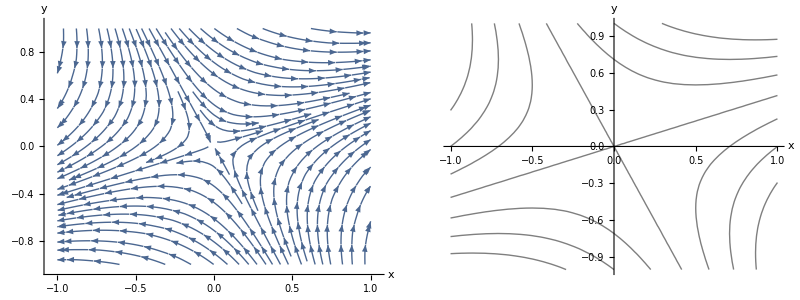

```mathematica
With[{colors=ColorData[97,"ColorList"]},Grid[{{StreamPlot[{x+y,x-y},{x,-1,1},{y,-1,1},Axes->True,Frame->False,AxesLabel->{x,y},ImageSize->Medium],
ContourPlot[-x^2+2 x y+y^2,{x,-1,1},{y,-1,1},Axes->True,Frame->False,AxesLabel->{x,y},ContourShading->False,ImageSize->Medium]}}]]
```

### Solution of Bernoulli Equation

The general form of the Bernoulli’s equation is

ⅆy/ⅆx+P(x)y=Q(x)y^n  (n≠0,1)

Direct solution using DSolve:

```mathematica
ⅆy/ⅆx+P[x]y==Q[x] y^n
SCMAF[%,SCDSolve,{All,y,x,ReplVar->{x',x''},Limit->Null,ReplConst->c},
Simplify,At[2],Post->{SCSimpExp,PowerExpand},ChangeSign->-1+n]
```

y P[x]+ⅆy/ⅆx==y^n Q[x]

y==(c ⅇ^(-(1-n) ∫^x P[x']ⅆ x')+ⅇ^(-(1-n) ∫^x P[x']ⅆ x') ∫^x ⅇ^((1-n) ∫^x'' P[x']ⅆ x') Q[x'']ⅆ x''-ⅇ^(-(1-n) ∫^x P[x']ⅆ x') n ∫^x ⅇ^((1-n) ∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')^(1/(1-n))

y==ⅇ^(-∫^x P[x']ⅆ x') (c+(1-n) ∫^x ⅇ^((1-n) ∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')^(1/(1-n))

Make the substitution v=y^(1-n) and we have

```mathematica
ⅆy/ⅆx+P[x]y==Q[x] y^n
SCMAF[%,SCEliminate,{All,v==y^(1-n),y},SCDerivExpand->v,Post->{PowerExpand,SCSimpExp},
SCDivEq,{All,v^(n/(1-n))/(1-n)},Post->SCSimpExp]
```

y P[x]+ⅆy/ⅆx==y^n Q[x]

v^(1/(1-n)) P[x]+v^(n/(1-n))/(1-n) ⅆv/ⅆx==v^(n/(1-n)) Q[x]

(1-n) v P[x]+ⅆv/ⅆx==(1-n) Q[x]

which is a linear equation and is soluble.

```mathematica
(1-n) v P[x]+ⅆv/ⅆx==(1-n) Q[x]
SCMAF[%,SCDSolve,{All,v,x,ReplVar->{x',x''},ReplConst->c,Limit->Null},Post->{Simplify,SCFactorInt,Simplify},ChangeSign->-1+n]
```

(1-n) v P[x]+ⅆv/ⅆx==(1-n) Q[x]

v==ⅇ^((-1+n) ∫^x P[x']ⅆ x') (c+(1-n) ∫^x ⅇ^((1-n) ∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')

The solution for y is then

```mathematica
y==v^(1/(1-n))
SCMAF[%,RA,{At[2],v==ⅇ^((-1+n) ∫^x P[x']ⅆ x') (c+(1-n) ∫^x ⅇ^((1-n) ∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')},Post->{SCSimpExp,PowerExpand}]
```

y==v^(1/(1-n))

y==ⅇ^(-∫^x P[x']ⅆ x') (c+(1-n) ∫^x ⅇ^((1-n) ∫^x'' P[x']ⅆ x') Q[x'']ⅆ x'')^(1/(1-n))

Example: Solve

ⅆy/ⅆx+y/x=2 x^3 y^4.

With the substitution v=y^(1-n)=y^-3 (n=4), the solution is

```mathematica
ⅆy/ⅆx+y/x==2 x^3 y^4
SCMAF[%,SCEliminate,{All,v==y^-3,y,Part->1},SCDerivExpand->v,Post->SCEqMerge,
SCCollectDerivs,{At[1],v,ⅆv/ⅆx},
SCDSolve,{All,v,x,ReplConst->c},
RA,{All,v==y^-3},Post->SCRecipEq,
SCSolve,{All,c,Post->Expand},Post->Reverse]
```

y/x+ⅆy/ⅆx==2 x^3 y^4

y^3==1/(c x^3-6 x^4)

6 x+1/(x^3 y^3)==c

Direct solution using SCDSolve:

```mathematica
ⅆy/ⅆx+y/x==2 x^3 y^4
SCMAF[%,SCDSolve,{All,y,x,ReplConst->c},Part->1,
SCEqMap,{All,#^3&},
SCSolve,{All,c,Post->Expand},Post->Reverse]
```

y/x+ⅆy/ⅆx==2 x^3 y^4

y^3==1/(c x^3-6 x^4)

6 x+1/(x^3 y^3)==c

Stream plot of the differential equation and the contour plot of the solution

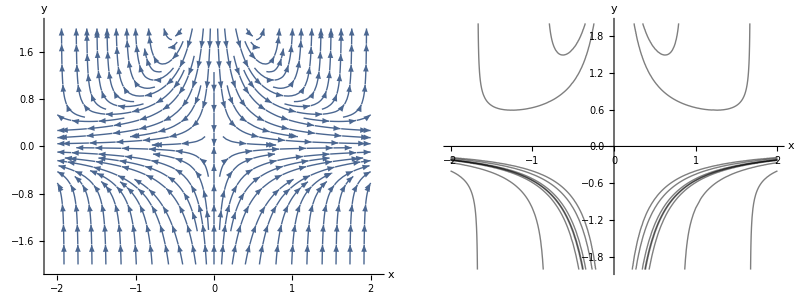

```mathematica
With[{colors=ColorData[97,"ColorList"]},Grid[{{StreamPlot[{x,y (-1+2 x^4 y^3)},{x,-2,2},{y,-2,2},Axes->True,Frame->False,AxesLabel->{x,y},ImageSize->Medium],
ContourPlot[6 x+1/(x^3 y^3),{x,-2,2},{y,-2,2},Axes->True,Frame->False,AxesLabel->{x,y},ContourShading->False,Contours->{-10,-5,-1,-0.1,0.1,1,5,10},ImageSize->Medium]}}]]
```

### Solution of Clairaut’s Equation y=x ⅆy/ⅆx-2(ⅆy/ⅆx)^2

Direct solution using DSolve:

```mathematica
y==x ⅆy/ⅆx-2(ⅆy/ⅆx)^2
SCMAF[%,SCDSolve,{All,y,x,ReplConst->c}]
```

y==x ⅆy/ⅆx-2 (ⅆy/ⅆx)^2

y==-2 c^2+c x

It will be seen that there is a singular solution that DSolve does not give.

Putting ⅆy/ⅆx=p and differentiating with respect to x, we obtain two solutions for p:

```mathematica
y==x ⅆy/ⅆx-2(ⅆy/ⅆx)^2
SCMAF[%,RA,{At[2],ⅆy/ⅆx==p},,
SCEqMap,{All,(ⅆ#)/ⅆx&},
SCDerivExpand,{At[2],p},RA->{All,ⅆy/ⅆx==p},
SCEqMerge,{All,Right},
SCDSolve,{All,p,x,ReplConst->c}]
```

y==x ⅆy/ⅆx-2 (ⅆy/ⅆx)^2

y==-2 p^2+p x

-4 p ⅆp/ⅆx+x ⅆp/ⅆx==0

{{p==x/4},{p==c}}

where c is an arbitrary constant.

The first solution gives the singular solution

```mathematica
y==-2 p^2+p x
SCMAF[%,RA,{At[2],p==x/4}]
```

y==-2 p^2+p x

y==x^2/8

The second solution gives the regular solution

```mathematica
y==-2 p^2+p x
SCMAF[%,RA,{At[2],p==c}]
```

y==-2 p^2+p x

y==-2 c^2+c x

The singular solution cannot be obtained from the regular solution for any value of c.

Actually, the singular solution is the envelope of the family of curves described by the regular solution.

```mathematica
{y-(-2 c^2+c x)==0,∂/(∂c)(y-(-2 c^2+c x))==0}
SCMAF[%,SCEvalDeriv,At[2],
SCEliminate,{All,c,Solve->y}]
```

{2 c^2-c x+y==0,(∂(2 c^2-c x+y))/(∂c)==0}

{2 c^2-c x+y==0,4 c-x==0}

y==x^2/8

Plot of the family of curves and the envelope

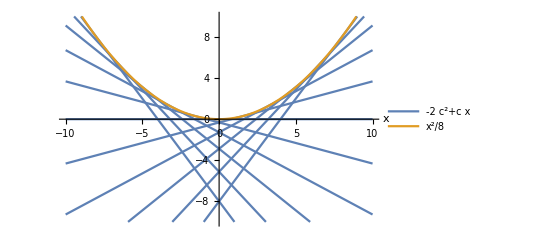

```mathematica
Module[{y1,y2},
y1[x]=Table[-2 c^2+c x,{c,-2,2,0.4}];
y2[x]=x^2/8;
Plot[{y1[x],y2[x]},{x,-10,10},AxesLabel->{"x"},PlotRange->{-10,10},PlotLegends->{"-2 c^2+c x","x^2/8"}]]
```

## Second-Order Linear Ordinary Differential Equations (ODEs)

A second-order linear ODE

y''+p(x)y'+q(x)y=r(x)

The equation is homogeneous if r(x)=0; nonhomogeneous otherwise.

Example: Homogeneous linear ODE

y''+y=0.

Example: Nonhomogeneous linear ODE

y''+y=1.

### Find a Basis if One Solution Is Known. Reduction of Order

If a solution y=y_1 of a homogenous equation is known, the substitution y=u y_1 reduces the order of the equation by 1, which may be soluble.

Example: Solve the ODE

y''-y'(x+1)/x+y/x=-x^2.

We observe that the sum of the coefficients of the differential equation is zero. It follows that one solution is y_1=ⅇ^x. Substituting y=u ⅇ^x gives

```mathematica
y''-y'(1+x)/x+y/x==-x^2
SCMAF[%,RA,{At[1],y==u ⅇ^x},Post->SCDerivExpand->{u,Prime->x},
SCCollectDerivs,{At[1],u,Post->{Simplify}},
SCDivEq,{All,ⅇ^x}]
```

y/x-((1+x) y')/x+y''==-x^2

(ⅇ^x (-1+x) u')/x+ⅇ^x u''==-x^2

((-1+x) u')/x+u''==-ⅇ^-x x^2

The solution for u' is

```mathematica
((-1+x) u')/x+u''==-ⅇ^-x x^2
SCMAF[%,SCDSolve,{All,u',x,ReplConst->-Subscript[c, 2]}]
```

((-1+x) u')/x+u''==-ⅇ^-x x^2

u'==-1/2 ⅇ^-x x^3-ⅇ^-x x c_2

and the solution for u is

```mathematica
u'==-1/2 ⅇ^-x x^3-ⅇ^-x x Subscript[c, 2]
SCMAF[%,SCDSolve,{All,u,x,Prime->x,ReplConst->Subscript[c, 1]},
Collect,{At[2],{Subscript[c, 1],Subscript[c, 2]},Factor}]
```

u'==-1/2 ⅇ^-x x^3-ⅇ^-x x c_2

u==c_1+1/2 ⅇ^-x (6+6 x+3 x^2+x^3+2 (1+x) c_2)

u==1/2 ⅇ^-x (6+6 x+3 x^2+x^3)+c_1+ⅇ^-x (1+x) c_2

and the solution y is

```mathematica
y==u ⅇ^x
SCMAF[%,RA,{At[2],u==1/2 ⅇ^-x (6+6 x+3 x^2+x^3)+Subscript[c, 1]+ⅇ^-x (1+x) Subscript[c, 2]},
SCExpandMult,At[2]]
```

y==ⅇ^x u

y==ⅇ^x (1/2 ⅇ^-x (6+6 x+3 x^2+x^3)+c_1+ⅇ^-x (1+x) c_2)

y==1/2 (6+6 x+3 x^2+x^3)+ⅇ^x c_1+(1+x) c_2

Direct solution using DSolve

```mathematica
y''-y'(1+x)/x+y/x==-x^2
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Subscript[c, 1],-Subscript[c, 2]}},ChangeSign->-1-x]
```

y/x-((1+x) y')/x+y''==-x^2

y==1/2 (6+6 x+3 x^2+x^3)+ⅇ^x c_1+(1+x) c_2

### Homogeneous Linear ODEs with Constant Coefficients

Second-order homogeneous linear ODEs whose coefficients a and b are constant

y''+a y'+b y=0

Substituting y=ⅇ^(λ x) gives

```mathematica
y''+a y'+b y==0
SCMAF[%,RA,{At[1],y==ⅇ^(λ x)},SCEvalDeriv->Prime->x,Post->Factor]
```

b y+a y'+y''==0

ⅇ^(x λ) (b+a λ+λ^2)==0

Hence if λ is a solution of the important characteristic equation (or auxiliary equation)

b+a λ+λ^2=0

The roots are

```mathematica
b+a λ+λ^2==0
SCMAF[%,SCSolve,{All,λ,ReplVar->{Subscript[λ, 2],Subscript[λ, 1]}},Post->Reverse]
```

b+a λ+λ^2==0

{λ_1==1/2 (-a+√(a^2-4 b)),λ_2==1/2 (-a-√(a^2-4 b))}

#### Case I. Two Distinct Real-Roots λ_1 and λ_2

The corresponding general solution is

y=c_1 ⅇ^(λ_1 x)+c_2 ⅇ^(λ_2 x)

Example: Solve

y''-y=0.

The characteristic equation is

```mathematica
y''-y==0
SCMAF[%,RA,{At[1],y==ⅇ^(λ x)},SCEvalDeriv->Prime->x,Post->Factor]
```

-y+y''==0

ⅇ^(x λ) (-1+λ) (1+λ)==0

The general solution is then

y=c_1 ⅇ^x+c_2 ⅇ^-x

#### Case II. Real Double Root λ=-a/2

If the discriminant a^2-4b is zero, we get only one root, λ=λ_1=λ_2=-a/2. The second solution can be obtained using the technique of reduction of order. Substituting y=u ⅇ^(-a x/2) gives

```mathematica
y''+a y'+b y==0
SCMAF[%,RA,{At[1],y==u ⅇ^(-a x/2)},SCDerivExpand->{u,Prime->x},
SCCollectDerivs,{At[1],u,u''},
RA,{At[1],-a^2/4+b==0},
SCDSolve,{All,u,x,ReplConst->{0,1}}]
```

b y+a y'+y''==0

u''==0

u==x

and therefore, the second solution is y_2=x ⅇ^(-a x/2). The general solution is then

```mathematica
y==Subscript[c, 1] ⅇ^(-(a x)/2)+Subscript[c, 2] x ⅇ^(-(a x)/2)
SCMAF[%,SCFactor,{At[2],ⅇ^(-(a x)/2)}]
```

y==ⅇ^(-(a x)/2) c_1+ⅇ^(-(a x)/2) x c_2

y==ⅇ^(-(a x)/2) (c_1+x c_2)

#### Case III. Complex Roots -1/2a+ⅈ ω and -1/2a-ⅈ ω

If the discriminant a^2-4b is negative, λ_1 and λ_2 are

```mathematica
{Subscript[λ, 1]==1/2 (-a+√(a^2-4 b)),Subscript[λ, 2]==1/2 (-a-√(a^2-4 b))}
SCMAF[%,SCFactorI,√(a^2-4 b),Expand->All,
RA,{All,√(-a^2+4 b)==2ω}]
```

{λ_1==1/2 (-a+√(a^2-4 b)),λ_2==1/2 (-a-√(a^2-4 b))}

{λ_1==-a/2+1/2 ⅈ √(-a^2+4 b),λ_2==-a/2-1/2 ⅈ √(-a^2+4 b)}

{λ_1==-a/2+ⅈ ω,λ_2==-a/2-ⅈ ω}

where

```mathematica
ω==1/2 √(-a^2+4 b)
SCMAF[%,SCEqMap,{All,#^2&},Expand->At[2]]
```

ω==1/2 √(-a^2+4 b)

ω^2==-a^2/4+b

Hence a real general solution in Case III is

```mathematica
y==ⅇ^(-a x/2)(Subscript[c, 1] ⅇ^(ⅈ ω x)+Subscript[c, 2] ⅇ^(-ⅈ ω x))
SCMAF[%,ExpToTrig,ⅇ^(ⅈ a_)|ⅇ^(-ⅈ a_),
Collect,{(Cos[x ω]+ⅈ Sin[x ω]) Subscript[c, 1]+(Cos[x ω]-ⅈ Sin[x ω]) Subscript[c, 2],{Cos[x ω],Sin[x ω]},Simplify},RA->{Subscript[c, 1]+Subscript[c, 2]==A,ⅈ (Subscript[c, 1]-Subscript[c, 2])==B}]
```

y==ⅇ^(-(a x)/2) (ⅇ^(ⅈ x ω) c_1+ⅇ^(-ⅈ x ω) c_2)

y==ⅇ^(-(a x)/2) ((Cos[x ω]+ⅈ Sin[x ω]) c_1+(Cos[x ω]-ⅈ Sin[x ω]) c_2)

y==ⅇ^(-(a x)/2) (A Cos[x ω]+B Sin[x ω])

### Nonhomogeneous Linear ODEs with Constant Coefficients

Second-order nonhomogeneous linear ODEs whose coefficients a and b are constant

y''+a y'+b y=f(x)

If f(x)=0, it becomes a homogeneous linear ODE.

Example: Solve

y''+3 y'+2y=x ⅇ^-x.

For the complementary solution, the trial solution is y=ⅇ^(λ x).

```mathematica
y''+3 y'+2y==0
SCMAF[%,RA,{At[1],y==ⅇ^(λ x)},SCEvalDeriv->Prime->x,Post->Factor]
```

2 y+3 y'+y''==0

ⅇ^(x λ) (1+λ) (2+λ)==0

which gives

y_h=c_1 ⅇ^-x+c_2 ⅇ^(-2x).

For the particular solution, using the technique of reduction of order, we put y=ⅇ^-x u.

```mathematica
y''+3 y'+2y==x ⅇ^-x
SCMAF[%,RA,{All,y==ⅇ^-x u},Post->{SCDivEq->ⅇ^-x,Factor,SCDerivExpand->{u,Prime->x}},
SCDSolve,{All,u',x,ReplConst->0},
SCDSolve,{All,u,x,ReplConst->0}]
```

2 y+3 y'+y''==ⅇ^-x x

u'==-1+x

u==-x+x^2/2

The general solution is then

```mathematica
y==Subscript[c, 1] ⅇ^-x+Subscript[c, 2] ⅇ^(-2x)+ⅇ^-x u
SCMAF[%,RA,{At[2],u==-x+x^2/2}]
```

y==ⅇ^-x u+ⅇ^-x c_1+ⅇ^(-2 x) c_2

y==ⅇ^-x (-x+x^2/2)+ⅇ^-x c_1+ⅇ^(-2 x) c_2

### Linear ODEs with Variable Coefficients

Example: Solve

x(1-x)y''+4 y'+2y=0

The equation is exact. The solution y is

```mathematica
x(1-x)y''+4 y'+2y==0
SCMAF[%,SCDerivSimp,{At[1],Prime->x},,
SCDSolve,{All,(-1+x)^6/x^2 ((x^3 y)/(-1+x)^5)',x,ReplConst->-Subscript[c, 2]},SCDivEq->(-1+x)^6/x^2,,
SCDSolve,{All,(x^3 y)/(-1+x)^5,x,ReplConst->-Subscript[c, 1]},
SCSolve,{All,y,Post->SCExpandMult},ChangeSign->-1+_]
```

2 y+4 y'+(1-x) x y''==0

-((-1+x)^6/x^2 ((x^3 y)/(-1+x)^5)')'==0

((x^3 y)/(-1+x)^5)'==-(x^2 c_2)/(-1+x)^6

(x^3 y)/(-1+x)^5==-c_1-((-1+5 x-10 x^2) c_2)/(30 (-1+x)^5)

y==((1-x)^5 c_1)/x^3+((1-5 x+10 x^2) c_2)/(30 x^3)

Direct solution using DSolve

```mathematica
x(1-x)y''+4 y'+2y==0
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Subscript[c, 1],Subscript[c, 2]}},ChangeSign->-1+x]
```

2 y+4 y'+(1-x) x y''==0

y==((1-x)^5 c_1)/x^3+((1-5 x+10 x^2) c_2)/(30 x^3)

## Higher-Order Ordinary Differential Equations (ODEs)

### The Wronskian

There is a simple test for the linear dependence of a set of differentiable functions. The Wronskian W(x) is defined as the determinant

W(x)=W[y_1(x),y_2(x),…,y_n(x)]
≡det|y_1 | y_2 | ⋯ | y_n
y'_1 | y'_2 | ⋯ | y'_n
⋯ | ⋯ | ⋯ | ⋯
y_1^(n-1) | y_2^(n-1) | ⋯ | y_n^(n-1)|

The Wronskian W(x) of any n solutions satisfies the simple first-order equation

W'(x)=-p_(n-1)(x)W(x)

The solution of this equation is known as Abel’s formula:

```mathematica
W'[x]==-Subscript[p, n-1][x]W[x]
SCMAF[%,SCDSolve,{All,W[x],x,ReplVar->x',ReplConst->A,Limit->Null}]
```

W'[x]==-W[x] p_(-1+n)[x]

W[x]==A ⅇ^(-∫^x p_(-1+n)[x']ⅆ x')

### Linear Equations with Constant Coefficients

Example: Solve

(ⅆ^2 y)/(ⅆ x^2)+y=x sin x.

The homogeneous solution

```mathematica
(ⅆ^2 y)/(ⅆ x^2)+y==0
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Subscript[c, 1],Subscript[c, 2]}},RA->y==Subscript[y, h][x]]
```

y+(ⅆ^2 y)/(ⅆ x^2)==0

y_h[x]==Cos[x] c_1+Sin[x] c_2

For the particular solution, we set the trial function

y=(a x+b)x sin x+(c x+d)x cos x

Note that x is multiplied to sin x and cos x since these are the homogeneous solutions. Substituting into the differential equation gives

```mathematica
(ⅆ^2 y)/(ⅆ x^2)+y==x Sin[x]
SCMAF[%,RA,{At[1],y==(a x+b)x Sin[x]+(c x+d)x Cos[x]},Post->SCEvalDeriv,
SCCollectPoly,{All,{x,Cos[x],Sin[x]},MatrixForm->True}]
```

y+(ⅆ^2 y)/(ⅆ x^2)==x Sin[x]

2 c Cos[x]+2 a x Cos[x]+2 (b+a x) Cos[x]+2 a Sin[x]-2 c x Sin[x]-2 (d+c x) Sin[x]==x Sin[x]

{2 b+2 c,2 a-2 d,4 a,-4 c}·(Cos[x]
Sin[x]
x Cos[x]
x Sin[x])=={0,0,0,1}·(Cos[x]
Sin[x]
x Cos[x]
x Sin[x])

Equating the coefficients and solving the equations gives

```mathematica
{2 b+2 c,2 a-2 d,4 a,-4 c}=={0,0,0,1}//Thread
SCMAF[%,SCSolve,{All,{a,b,c,d}}]
```

{2 b+2 c==0,2 a-2 d==0,4 a==0,-4 c==1}

{a==0,b==1/4,c==-1/4,d==0}

The particular solution is therefore

```mathematica
Subscript[y, p][x]==(a x+b)x Sin[x]+(c x+d)x Cos[x]
SCMAF[%,RA,{At[2],{a==0,b==1/4,c==-1/4,d==0}},Post->Expand]
```

y_p[x]==x (d+c x) Cos[x]+x (b+a x) Sin[x]

y_p[x]==-1/4 x^2 Cos[x]+1/4 x Sin[x]

The full solution is

```mathematica
y[x]==Subscript[y, h][x]+Subscript[y, p][x]
SCMAF[%,RA,{At[2],{Subscript[y, h][x]==Cos[x] Subscript[c, 1]+Sin[x] Subscript[c, 2],Subscript[y, p][x]==-1/4 x^2 Cos[x]+1/4 x Sin[x]}}]
```

y[x]==y_h[x]+y_p[x]

y[x]==-1/4 x^2 Cos[x]+1/4 x Sin[x]+Cos[x] c_1+Sin[x] c_2

Direct solution using DSolve:

```mathematica
(ⅆ^2 y)/(ⅆ x^2)+y==x Sin[x]
SCMAF[%,SCDSolve,{All,y[x],x,ReplConst->{Subscript[c, 1]',Subscript[c, 2]},Post->Expand},
SCTrigToHalf,{{Cos[2x],Sin},{Sin[2x]}},Expand->At[2],
SCTrigConvert,{Cos[x]^2,Sin},Expand->At[2],
SCFactor,{Cos[x]/8+Cos[x] Subscript[c, 1]',Cos[x]},RA->1/8+Subscript[c, 1]'==Subscript[c, 1]]
```

y+(ⅆ^2 y)/(ⅆ x^2)==x Sin[x]

y[x]==Cos[x]/8-1/4 x^2 Cos[x]+1/4 x Sin[x]+Sin[x] c_2+Cos[x] c'_1

y[x]==-1/4 x^2 Cos[x]+1/4 x Sin[x]+Cos[x] c_1+Sin[x] c_2

### Method of Variation of Parameters

Suppose we wish to find a particular integral of the equation

a_n(x)(ⅆ^n y)/(ⅆ x^n)+⋯+a_1(x)ⅆy/ⅆx+a_0(x)y=f(x)

and the complementary function y_c(x) is

y_c(x)=c_1 y_1(x)+c_2 y_2(x)+⋯+c_n y_n(x),

where the functions y_j(x) are known. We then assume a particular integral of the form

y_p(x)=k_1(x)y_1(x)+k_2(x)y_2(x)+⋯+k_n(x)y_n(x).

and determine the coefficient functions k_j(x). Since we have n arbitrary functions k_1(x), k_2(x), …, k_n(x), but only one restriction on them (namely the ODE), we may impose a further n-1 constraints:

k'_1(x)y_1(x)+k'_2(x)y_2(x)+⋯+k'_n(x)y_n(x)=0
k'_1(x)y'_1(x)+k'_2(x)y'_2(x)+⋯+k'_n(x)y'_n(x)=0
⋮
k'_1(x)y_1^(n-2)(x)+k'_2(x)y_2^(n-2)(x)+⋯+k'_n(x)y_n^(n-2)(x)=0

Example: Use the variation-of-parameters method to solve

(ⅆ^2 y)/(ⅆ x^2)+y=cosec x,    y(0)=y(π/2)=0.

The complementary function is

```mathematica
(ⅆ^2 y)/(ⅆ x^2)+y==0
SCMAF[%,SCDSolve,{All,y[x],x,ReplConst->{Subscript[c, 2],Subscript[c, 1]}},RA->y==Subscript[y, c]]
```

y+(ⅆ^2 y)/(ⅆ x^2)==0

y_c[x]==Sin[x] c_1+Cos[x] c_2

We therefore assume a particular integral of the form

```mathematica
Subscript[y, p][x]==Subscript[k, 1][x]Subscript[y, 1][x]+Subscript[k, 2][x]Subscript[y, 2][x]
SCMAF[%,RA,{At[2],{Subscript[y, 1][x]==Sin[x],Subscript[y, 2][x]==Cos[x]}}]
```

y_p[x]==k_1[x] y_1[x]+k_2[x] y_2[x]

y_p[x]==Sin[x] k_1[x]+Cos[x] k_2[x]

The one constraint on k_1(x) and k_2(x) and their derivatives are

```mathematica
Sin[x] Subscript[k, 1]'[x]+Cos[x] Subscript[k, 2]'[x]==0
SCMAF[%,SCApplyFunc,{At[1],D->x}]
```

Sin[x] k'_1[x]+Cos[x] k'_2[x]==0

Cos[x] k'_1[x]-Sin[x] k'_2[x]+Sin[x] k''_1[x]+Cos[x] k''_2[x]==0

Substitution in the ODE gives

```mathematica
(ⅆ^2 y)/(ⅆ x^2)+y==Csc[x]
SCMAF[%,RA,{At[1],y[x]==Sin[x] Subscript[k, 1][x]+Cos[x] Subscript[k, 2][x]},Post->SCEvalDeriv,
SCEliminate,{At[1],Cos[x] Subscript[k, 1]'[x]-Sin[x] Subscript[k, 2]'[x]+Sin[x] Subscript[k, 1]''[x]+Cos[x] Subscript[k, 2]''[x]==0,Sin[x] Subscript[k, 1]''[x]+Cos[x] Subscript[k, 2]''[x]}]
```

y+(ⅆ^2 y)/(ⅆ x^2)==Csc[x]

2 Cos[x] k'_1[x]-2 Sin[x] k'_2[x]+Sin[x] k''_1[x]+Cos[x] k''_2[x]==Csc[x]

Cos[x] k'_1[x]-Sin[x] k'_2[x]==Csc[x]

The solutions for k_1(x) and k_2(x) are

```mathematica
{Sin[x] Subscript[k, 1]'[x]+Cos[x] Subscript[k, 2]'[x]==0,Cos[x] Subscript[k, 1]'[x]-Sin[x] Subscript[k, 2]'[x]==Csc[x]}
SCMAF[%,SCSolve,{All,{Subscript[k, 1]'[x],Subscript[k, 2]'[x]},Post->Simplify},
SCDSolve,{All,{Subscript[k, 1][x],Subscript[k, 2][x]},x,ReplConst->{0,0}}]
```

{Sin[x] k'_1[x]+Cos[x] k'_2[x]==0,Cos[x] k'_1[x]-Sin[x] k'_2[x]==Csc[x]}

{k'_1[x]==Cot[x],k'_2[x]==-1}

{k_1[x]==Log[Sin[x]],k_2[x]==-x}

The general solution is therefore,

```mathematica
y[x]==Subscript[y, c][x]+Subscript[y, p][x]
SCMAF[%,RR,{At[2],{Subscript[y, c][x]==Sin[x] Subscript[c, 1]+Cos[x] Subscript[c, 2],Subscript[y, p][x]==Subscript[k, 1][x]Sin[x]+Subscript[k, 2][x]Cos[x],Subscript[k, 1][x]==Log[Sin[x]],Subscript[k, 2][x]==-x}}]
```

y[x]==y_c[x]+y_p[x]

y[x]==-x Cos[x]+Log[Sin[x]] Sin[x]+Sin[x] c_1+Cos[x] c_2

Applying the boundary conditions, we find

```mathematica
{y[0]==0,y[π/2]==0}
SCMAF[%,RA,{At[1],y[0]==lim_(x->0) y[x]},
RA,{All,y[x_]==-x Cos[x]+Log[Sin[x]] Sin[x]+Sin[x] Subscript[c, 1]+Cos[x] Subscript[c, 2]},Post->SCEvalLimit]
```

{y[0]==0,y[π/2]==0}

{lim_(x→0) y[x]==0,y[π/2]==0}

{c_2==0,c_1==0}

and so

```mathematica
y[x]==-x Cos[x]+Log[Sin[x]] Sin[x]+Sin[x] Subscript[c, 1]+Cos[x] Subscript[c, 2]
SCMAF[%,RA,{At[2],{Subscript[c, 2]==0,Subscript[c, 1]==0}}]
```

y[x]==-x Cos[x]+Log[Sin[x]] Sin[x]+Sin[x] c_1+Cos[x] c_2

y[x]==-x Cos[x]+Log[Sin[x]] Sin[x]

Plot of y(x)

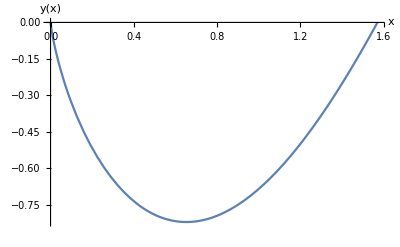

```mathematica
Module[{x,y},
y[x]=-x Cos[x]+Log[Sin[x]] Sin[x];
Plot[y[x],{x,0,π/2},AxesLabel->{"x","y(x)"}]]
```

Example: Use the variation-of-parameters method to solve

y''+3 y'+2y=exp[ⅇ^x].

For the complementary solution, the trial solution is y=ⅇ^(λ x).

```mathematica
y''+3 y'+2y==0
SCMAF[%,RA,{At[1],y==ⅇ^(λ x)},SCEvalDeriv->Prime->x,Post->Factor]
```

2 y+3 y'+y''==0

ⅇ^(x λ) (1+λ) (2+λ)==0

which gives

y=c_1 ⅇ^-x+c_2 ⅇ^(-2x)

Then put

y=k_1(x)ⅇ^-x+k_2(x)ⅇ^(-2x)

We differentiate, obtaining

```mathematica
SCARA[y',y==Subscript[k, 1][x] ⅇ^-x+Subscript[k, 2][x] ⅇ^(-2x),SCEvalDeriv->Prime->x]
```

y'==-ⅇ^-x k_1[x]-2 ⅇ^(-2 x) k_2[x]+ⅇ^-x k'_1[x]+ⅇ^(-2 x) k'_2[x]

and impose the condition

ⅇ^-x k'_1(x)+ⅇ^(-2 x) k'_2(x)=0

Then

y'=-ⅇ^-x k_1(x)-2 ⅇ^(-2 x) k_2(x)

and

```mathematica
SCAFE[y'',SCTransFunc,{All,y'==-ⅇ^-x Subscript[k, 1][x]-2 ⅇ^(-2 x) Subscript[k, 2][x]},SCEvalDeriv->Prime->x]
```

y''==ⅇ^-x k_1[x]+4 ⅇ^(-2 x) k_2[x]-ⅇ^-x k'_1[x]-2 ⅇ^(-2 x) k'_2[x]

Substituting into the differential equation, we obtain

```mathematica
{y''+3 y'+2y==Exp[ⅇ^x],ⅇ^-x Subscript[k, 1]'[x]+ⅇ^(-2 x) Subscript[k, 2]'[x]==0}
SCMAF[%,RA,{At[1],{y==Subscript[k, 1][x] ⅇ^-x+Subscript[k, 2][x] ⅇ^(-2x),y'==-ⅇ^-x Subscript[k, 1][x]-2 ⅇ^(-2 x) Subscript[k, 2][x],y''==ⅇ^-x Subscript[k, 1][x]+4 ⅇ^(-2 x) Subscript[k, 2][x]-ⅇ^-x Subscript[k, 1]'[x]-2 ⅇ^(-2 x) Subscript[k, 2]'[x]}},Post->Expand,
SCSolve,{All,{Subscript[k, 1]'[x],Subscript[k, 2]'[x]}},
SCDSolve,{All,{Subscript[k, 1][x],Subscript[k, 2][x]},x,ReplConst->{Subscript[c, 1],Subscript[c, 2]}}]
```

{2 y+3 y'+y''==ⅇ^(ⅇ^x),ⅇ^-x k'_1[x]+ⅇ^(-2 x) k'_2[x]==0}

{k'_1[x]==ⅇ^(ⅇ^x+x),k'_2[x]==-ⅇ^(ⅇ^x+2 x)}

{k_1[x]==ⅇ^(ⅇ^x)+c_1,k_2[x]==-ⅇ^(ⅇ^x) (-1+ⅇ^x)+c_2}

Note that using the substitution t=ⅇ^x,

```mathematica
{Subscript[k, 1]'[x]==ⅇ^(ⅇ^x+x),Subscript[k, 2]'[x]==-ⅇ^(ⅇ^x+2 x)}
SCMAF[%,SCEqMap,{All,∫#ⅆx&},Level->1,SCEvalInt->At[_,1],Plus->{At[1,2],Subscript[c, 1]},Plus->{At[2,2],Subscript[c, 2]},
SCTransInt,{All,TransVar->{x,t,t==ⅇ^x}},
SCEvalInt,All,RA->t==ⅇ^x]
```

{k'_1[x]==ⅇ^(ⅇ^x+x),k'_2[x]==-ⅇ^(ⅇ^x+2 x)}

{k_1[x]==∫ⅇ^(ⅇ^x+x)ⅆx+c_1,k_2[x]==-∫ⅇ^(ⅇ^x+2 x)ⅆx+c_2}

{k_1[x]==∫ⅇ^t ⅆt+c_1,k_2[x]==-∫ⅇ^t tⅆt+c_2}

{k_1[x]==ⅇ^(ⅇ^x)+c_1,k_2[x]==-ⅇ^(ⅇ^x) (-1+ⅇ^x)+c_2}

Then the general solution is

```mathematica
y==Subscript[k, 1][x] ⅇ^-x+Subscript[k, 2][x] ⅇ^(-2x)
SCMAF[%,RA,{At[2],{Subscript[k, 1][x]==ⅇ^(ⅇ^x)+Subscript[c, 1],Subscript[k, 2][x]==-ⅇ^(ⅇ^x) (-1+ⅇ^x)+Subscript[c, 2]}},Post->Expand]
```

y==ⅇ^-x k_1[x]+ⅇ^(-2 x) k_2[x]

y==ⅇ^(ⅇ^x-2 x)+ⅇ^-x c_1+ⅇ^(-2 x) c_2

Direct solution using DSolve

```mathematica
y''+3 y'+2y==Exp[ⅇ^x]
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Subscript[c, 1],Subscript[c, 2]}}]
```

2 y+3 y'+y''==ⅇ^(ⅇ^x)

y==ⅇ^(ⅇ^x-2 x)+ⅇ^(-2 x) c_1+ⅇ^-x c_2

### Autonomous Equations

An autonomous equation is one whose independent variable does not appear explicitly,  except in ⅆ/ⅆx, ⅆ^2/ⅆ x^2 etc., then we make the substitution p=ⅆy/ⅆx but also write

```mathematica
SCAFE[{(ⅆ^2 y)/(ⅆ x^2),(ⅆ^3 y)/(ⅆ x^3)},SCSepDerivs,All,RA->ⅆy/ⅆx==p,PostAll->Thread,
SCTransDeriv,{At[_,2],TransVar->{x,y}},RA->ⅆy/ⅆx==p,SCDerivExpand->p,Post->Expand]
```

{(ⅆ^2 y)/(ⅆ x^2)==ⅆp/ⅆx,(ⅆ^3 y)/(ⅆ x^3)==ⅆ/ⅆx ⅆp/ⅆx}

{(ⅆ^2 y)/(ⅆ x^2)==p ⅆp/ⅆy,(ⅆ^3 y)/(ⅆ x^3)==p (ⅆp/ⅆy)^2+p^2 (ⅆ^2 p)/(ⅆ y^2)}

and so on for higher derivatives. This leads to an equation of one order lower.

Example: Solve

1+y(ⅆ^2 y)/(ⅆ x^2)+(ⅆy/ⅆx)^2=0.

Making the substitutions ⅆy/ⅆx=p, we obtain the first-order ODE

```mathematica
1+y(ⅆ^2 y)/(ⅆ x^2)+(ⅆy/ⅆx)^2==0
SCMAF[%,SCSepDerivs,At[1],RA->ⅆy/ⅆx==p,
SCTransDeriv,{At[1],TransVar->{x,y}},RA->ⅆy/ⅆx==p,
SCDSolve,{All,p,y,ReplConst->Log[Subscript[c, 1]]},
SCDivNum,{All,y,Positive->True},RA->p==ⅆy/ⅆx]
```

1+(ⅆy/ⅆx)^2+y (ⅆ^2 y)/(ⅆ x^2)==0

{{p==-(√(-y^2+c_1^2))/y},{p==(√(-y^2+c_1^2))/y}}

{{ⅆy/ⅆx==-√(-1+c_1^2/y^2)},{ⅆy/ⅆx==√(-1+c_1^2/y^2)}}

i.e.,

ⅆy/ⅆx=(±1)√(c_1^2/y^2-1)

which gives

```mathematica
ⅆy/ⅆx==(±1)√(-1+Subscript[c, 1]^2/y^2)
SCMAF[%,SCRecipDeriv,At[1],
SCRecipEq,All,
SCDSolve,{All,x,y,ReplConst->-Subscript[c, 2]},
SCMoveTerm,{All,Subscript[c, 2]},
SCEqMap,{All,#^2&},Post->{At[2],Expand},
SCMoveTerm,{All,y^2}]
```

ⅆy/ⅆx==(±1) √(-1+c_1^2/y^2)

(x+c_2)^2==-y^2+c_1^2

y^2+(x+c_2)^2==c_1^2

Direct solution using SCDSolve:

```mathematica
1+y(ⅆ^2 y)/(ⅆ x^2)+(ⅆy/ⅆx)^2==0
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Log[Subscript[c, 1]],Subscript[c, 2]}},
Simplify,-x^2-2 x Subscript[c, 2]-Subscript[c, 2]^2]
```

1+(ⅆy/ⅆx)^2+y (ⅆ^2 y)/(ⅆ x^2)==0

{{y==-√(-x^2+c_1^2-2 x c_2-c_2^2)},{y==√(-x^2+c_1^2-2 x c_2-c_2^2)}}

{{y==-√(c_1^2-(x+c_2)^2)},{y==√(c_1^2-(x+c_2)^2)}}

which gives

```mathematica
y==±√(Subscript[c, 1]^2-(x+Subscript[c, 2])^2)
SCMAF[%,SCSolve,{All,(x+Subscript[c, 2])^2},SCMoveTerm->y^2]
```

y==±√(c_1^2-(x+c_2)^2)

y^2+(x+c_2)^2==c_1^2

Example: Solve

a^2 y''^2=(1+y'^2)^3.

Put p=y'. The solutions for p' are

```mathematica
a^2 y''^2==(1+y'^2)^3
SCMAF[%,SCTransFunc,{All,y'==p},
SCSolve,{All,p'}]
```

a^2 y''^2==(1+y'^2)^3

a^2 p'^2==(1+p^2)^3

{{p'==-((1+p^2)^(3/2))/a},{p'==((1+p^2)^(3/2))/a}}

i.e.,

p'=(±1) ((p^2+1)^(3/2))/a

which gives

```mathematica
p'==(±1) ((1+p^2)^(3/2))/a
SCMAF[%,SCDivEq,{All,((1+p^2)^(3/2))/a},Post->SCEqMerge,
SCDerivSimp,{At[1],Prime->x}]
```

p'==(±1) ((1+p^2)^(3/2))/a

-(±1)+(a p')/((1+p^2)^(3/2))==0

((a p)/(√(1+p^2))-(±1) x)'==0

Then we have

```mathematica
(a p)/(√(1+p^2))-(±1) x==Subscript[c, 1]
SCMAF[%,SCSolve,{All,1+p^2},
SCDivDenom,{At[2],(±1)^2},RA->(±1) Subscript[c, 1]==-Subscript[c, 1],
SCSolve,{All,p^2,Post->Together},Hold->x-Subscript[c, 1],ChangeSign-> -a^2+_,RA->p==y']
```

(a p)/(√(1+p^2))-(±1) x==c_1

1+p^2==(a^2 p^2)/(x-c_1)^2

y'^2==(x-c_1)^2/(a^2-(x-c_1)^2)

and

```mathematica
y'==(±1)(x-Subscript[c, 1])/(√(a^2-(x-Subscript[c, 1])^2))
SCMAF[%,SCDSolve,{All,y,x,ReplConst->Subscript[c, 2]},Post->{Simplify,-x^2+2 x Subscript[c, 1]-Subscript[c, 1]^2},
SCSolve,{All,(x-Subscript[c, 1])^2},Post->{Simplify,-y^2+2 y Subscript[c, 2]-Subscript[c, 2]^2},
SCEqMove,{All,a^2,Right}]
```

y'==(±1) (x-c_1)/(√(a^2-(x-c_1)^2))

(x-c_1)^2==a^2-(y-c_2)^2

(x-c_1)^2+(y-c_2)^2==a^2

Direct solution using DSolve

```mathematica
a^2 y''^2==(1+y'^2)^3
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Subscript[c, 1]/a,Subscript[c, 2]}},
SCMoveTerm,{All,Subscript[c, 2]},Level->{2},Post->{SCEqMove->{a^2,Right},Simplify,-x^2+a_ x Subscript[c, 1]-Subscript[c, 1]^2,Expand,-x^2+_,SCEqMap->(#^2&)},
SCChange,{All,(x-Subscript[c, 1])^2+(y-Subscript[c, 2])^2==a^2}]
```

a^2 y''^2==(1+y'^2)^3

{{(x-c_1)^2+(y-c_2)^2==a^2},{(x-c_1)^2+(y-c_2)^2==a^2},{(x+c_1)^2+(y-c_2)^2==a^2},{(x+c_1)^2+(y-c_2)^2==a^2}}

(x-c_1)^2+(y-c_2)^2==a^2

### Eigenvalue Problems

An eigenvalue problem is a boundary-value problem that has nontrivial solutions only when a parameter E that enters the problem has special values called eigenvalues.

Example: Consider the boundary-value problem

y''+k^2 y=0,    (k>0),    y(0)=0,y(1)=0.

The solution of ODE subject to the constraint y(0)=0 is

```mathematica
y''+k^2 y==0
SCMAF[%,SCDSolve,{All,y[0]==0,y,x,ReplConst->A}]
```

k^2 y+y''==0

y==A Sin[k x]

The second constraint y(1)=0 then gives sin k=0, and therefore, k=n π (n=1,2,…).

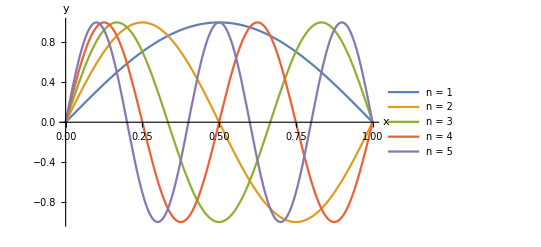

```mathematica
Module[{tbl},
tbl=Table[Sin[n π x],{n,1,5}];
Plot[tbl,{x,0,1},AxesLabel->{"x","y"},PlotLegends->Table["n = "<>ToString[n],{n,5}]]]
```

Example: Eigenvalue problem having transcendental eigenvalues. Consider the eigenvalue problem

y''+(E-x) y=0,    y(0)=0,y(∞)=0.

for 0<x<∞. The solutions are Airy functions:

```mathematica
y''+(Ε-x) y==0
SCMAF[%,SCDSolve,{All,y,x,ReplConst->{Subscript[c, 1],Subscript[c, 2]}}]
```

y (-x+Ε)+y''==0

y==AiryAi[x-Ε] c_1+AiryBi[x-Ε] c_2

Plot of Airy functions Ai(x) and Bi(x)

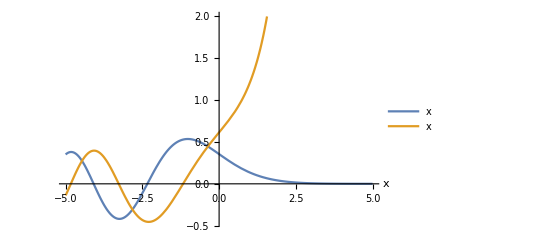

```mathematica
Plot[{AiryAi[x],AiryBi[x]},{x,-5,5},AxesLabel->{"x"},PlotRange->{Automatic,2}, PlotLegends->"Expressions"]
```

The general solution that vanishes as x→+∞ is, with c_1=A, c_2=0,

y=A Ai(x-E).

The boundary condition y(0)=0 gives the eigenvalue condition

```mathematica
y[0]==0
SCMAF[%,RA,{At[1],y[x_]==A AiryAi[x-Ε]},SCDivide->A]
```

y[0]==0

AiryAi[-Ε]==0

The Airy function Ai(-E) is a transcendental function whose zeros may be computed numerically.

```mathematica
AiryAi[-Ε]==0
SCMAF[%,SCFindAllRoots,{All,{Ε,0,10,0.1}}]
```

AiryAi[-Ε]==0

Ε=={2.33811,4.08795,5.52056,6.78671,7.94413,9.02265}

Using the asymptotic expansion of Ai(-E),

```mathematica
AiryAi[-Ε]==0
SCMAF[%,SCAsympSeries,{At[1],1,Assumptions->Arg[-Ε]==π},Head->TildeTilde]
```

AiryAi[-Ε]==0

1/(√π Ε^(1/4)) Sin[π/4+(2 Ε^(3/2))/3]≈0

the approximate solution is

```mathematica
π/4+(2 Ε^(3/2))/3==n π
SCMAF[%,SCSolve,{All,Ε},Head->TildeTilde]
```

π/4+(2 Ε^(3/2))/3==n π

Ε≈1/4 (-1+4 n)^(2/3) (3 π)^(2/3)

with n=1,2,3,…. The numerical values are

```mathematica
N@Table[1/4 (-1+4 n)^(2/3) (3 π)^(2/3),{n,1,6}]
```

{2.32025,4.08181,5.51716,6.78445,7.94249,9.02137}

The error is less than 1%.

## Systems of Ordinary Differential Equations (ODEs)

Example: Consider the differential equations

y'_1=2/100 y_2-2/100 y_1
y'_2=2/100 y_1-2/100 y_2    y_1(0)=0,y_2(0)=150,

which can be put in matrix form:

```mathematica
{Subscript[y, 1]'==2/100 Subscript[y, 2]-2/100 Subscript[y, 1],Subscript[y, 2]'==2/100 Subscript[y, 1]-2/100 Subscript[y, 2]}
SCMAF[%,SCEqsMatForm,{All,{Subscript[y, 1],Subscript[y, 2]}}]
```

{y'_1==-y_1/50+y_2/50,y'_2==y_1/50-y_2/50}

(y'_1
y'_2)==(-1/50 | 1/50
1/50 | -1/50)·(y_1
y_2)

Plot of the direction field and the solution curve passing through the initial point (0,150)

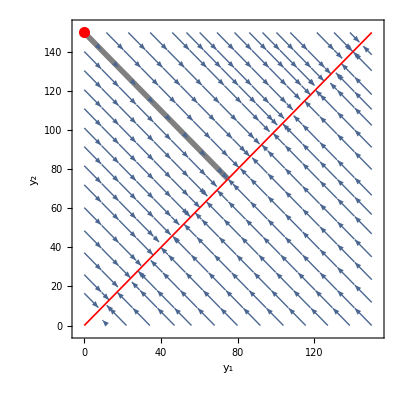

```mathematica
Module[{y1p,y2p},
y1p=-y1/50+y2/50;
y2p=y1/50-y2/50;
StreamPlot[{y1p,y2p},{y1,0,150},{y2,0,150},FrameLabel->{"y_1","y_2"},Epilog->{Thickness[0.01],Gray,Line[{{0,150},{150/2,150/2}}],Thickness[0.003],Red,Line[{{0,0},{150,150}}],PointSize[0.02],Red,Point[{0,150}]}]]
```

The eigenvalues and eigenvectors

```mathematica
Eigensystem[({{-1/50, 1/50}, {1/50, -1/50}})]
```

{{-1/25,0},{{-1,1},{1,1}}}

We put

λ_1=-1/25,    λ_2=0,    x^1={-1,1},    x^2={1,1}.

The general solution is

```mathematica
y⃗==Subscript[c, 1](x⃗)^1 ⅇ^(Subscript[λ, 1] t)+Subscript[c, 2](x⃗)^2 ⅇ^(Subscript[λ, 2] t)
SCMAF[%,RA,{All,{y⃗=={Subscript[y, 1][t],Subscript[y, 2][t]},Subscript[λ, 1]==-1/25,Subscript[λ, 2]==0,(x⃗)^1=={-1,1},(x⃗)^2=={1,1}}},Post->Thread]
```

y⃗==ⅇ^(t λ_1) (x⃗)^1 c_1+ⅇ^(t λ_2) (x⃗)^2 c_2

{y_1[t]==-ⅇ^(-t/25) c_1+c_2,y_2[t]==ⅇ^(-t/25) c_1+c_2}

The constants c_1, c_2 are determined from the initial conditions.

```mathematica
{Subscript[y, 1][0]==0,Subscript[y, 2][0]==150}
SCMAF[%,RA,{All,{Subscript[y, 1][t_]==-ⅇ^(-t/25) Subscript[c, 1]+Subscript[c, 2],Subscript[y, 2][t_]==ⅇ^(-t/25) Subscript[c, 1]+Subscript[c, 2]}},
SCSolve,{All,{Subscript[c, 1],Subscript[c, 2]}}]
```

{y_1[0]==0,y_2[0]==150}

{-c_1+c_2==0,c_1+c_2==150}

{c_1==75,c_2==75}

The solution

```mathematica
{Subscript[y, 1][t]==-ⅇ^(-t/25) Subscript[c, 1]+Subscript[c, 2],Subscript[y, 2][t]==ⅇ^(-t/25) Subscript[c, 1]+Subscript[c, 2]}
SCMAF[%,RA,{All,{Subscript[c, 1]==75,Subscript[c, 2]==75}},SCFactor->{At[_,2],75}]
```

{y_1[t]==-ⅇ^(-t/25) c_1+c_2,y_2[t]==ⅇ^(-t/25) c_1+c_2}

{y_1[t]==75 (1-ⅇ^(-t/25)),y_2[t]==75 (1+ⅇ^(-t/25))}

Direct solution

```mathematica
{Subscript[y, 1]'==2/100 Subscript[y, 2]-2/100 Subscript[y, 1],Subscript[y, 2]'==2/100 Subscript[y, 1]-2/100 Subscript[y, 2],Subscript[y, 1][0]==0,Subscript[y, 2][0]==150}
SCMAF[%,SCDSolve,{All,{Subscript[y, 1][t],Subscript[y, 2][t]},t,Post->Simplify},SCFactor->{At[1,2],75}]
```

{y'_1==-y_1/50+y_2/50,y'_2==y_1/50-y_2/50,y_1[0]==0,y_2[0]==150}

{y_1[t]==75 (1-ⅇ^(-t/25)),y_2[t]==75 (1+ⅇ^(-t/25))}

Plot of the solution

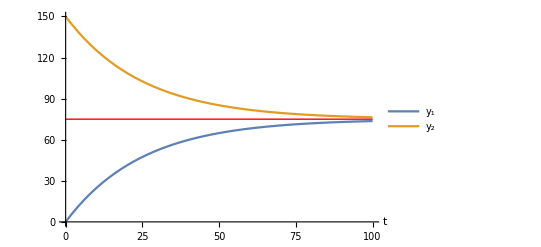

```mathematica
Module[{t,y1,y2},
y1[t_]=75 (1-ⅇ^(-t/25));
y2[t_]=75 (1+ⅇ^(-t/25));
Plot[{y1[t],y2[t]},{t,0,100},AxesLabel->{"t"},PlotLegends->{Subscript[y, 1],Subscript[y, 2]},Epilog->{Red,Line[{{0,150/2},{100,150/2}}]}]]
```

Example: Nonlinear system having a limit cycle. The nonlinear system is

(ẏ)_1=y_1+y_2-y_1(y_1^2+y_2^2),    (ẏ)_2=y_2-y_2(y_1^2+y_2^2)-y_1,     OverDot[■]≡ⅆ/ⅆt

The critical point is at (0,0).

```mathematica
{Subscript[ẏ, 1]==0,Subscript[ẏ, 2]==0}
SCMAF[%,RA,{All,{Subscript[ẏ, 1]==Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 1](Subscript[y, 1]^2+Subscript[y, 2]^2),Subscript[ẏ, 2]==-Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 2](Subscript[y, 1]^2+Subscript[y, 2]^2)}},
SCSolve,{All,{Subscript[y, 1],Subscript[y, 2]}}]
```

{(ẏ)_1==0,(ẏ)_2==0}

{y_1+y_2-y_1 (y_1^2+y_2^2)==0,-y_1+y_2-y_2 (y_1^2+y_2^2)==0}

{y_1==0,y_2==0}

For small displacement near (0,0),

```mathematica
{Subscript[ẏ, 1]==Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 1](Subscript[y, 1]^2+Subscript[y, 2]^2),Subscript[ẏ, 2]==-Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 2](Subscript[y, 1]^2+Subscript[y, 2]^2)}
SCMAF[%,SCTaylorSeries,{At[_,2],{Subscript[y, 1],Subscript[y, 2]}},
SCEqsMatForm,{All,{Subscript[y, 1],Subscript[y, 2]}}]
```

{(ẏ)_1==y_1+y_2-y_1 (y_1^2+y_2^2),(ẏ)_2==-y_1+y_2-y_2 (y_1^2+y_2^2)}

{(ẏ)_1==y_1+y_2,(ẏ)_2==-y_1+y_2}

((ẏ)_1
(ẏ)_2)==(1 | 1
-1 | 1)·(y_1
y_2)

The eigenvalues are

```mathematica
Eigenvalues[({{1, 1}, {-1, 1}})]
```

{1+ⅈ,1-ⅈ}

Therefore, (0,0) is a unstable spiral point with clockwise rotation.

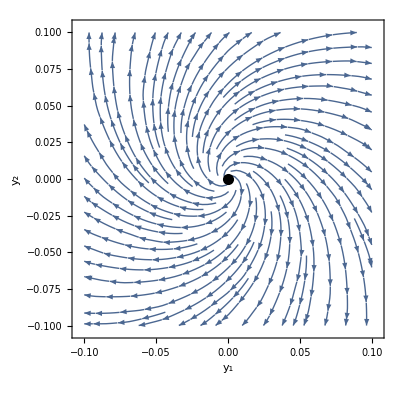

```mathematica
Module[{y1p,y2p},
y1p=y1+y2;
y2p=-y1+y2;
StreamPlot[{y1p,y2p},{y1,-0.1,0.1},{y2,-0.1,0.1},FrameLabel->{Subscript[y, 1],Subscript[y, 2]},Epilog->{PointSize[0.02],Point[{0,0}]}]]
```

Next, we examine the system behavior at ∞. For large y_1 and y_2, the linear terms can be ignored.

```mathematica
{Subscript[ẏ, 1]==Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 1](Subscript[y, 1]^2+Subscript[y, 2]^2),Subscript[ẏ, 2]==-Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 2](Subscript[y, 1]^2+Subscript[y, 2]^2)}
SCMAF[%,RA,{All,{Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 1](Subscript[y, 1]^2+Subscript[y, 2]^2)->-Subscript[y, 1](Subscript[y, 1]^2+Subscript[y, 2]^2),-Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 2](Subscript[y, 1]^2+Subscript[y, 2]^2)->-Subscript[y, 2](Subscript[y, 1]^2+Subscript[y, 2]^2)}},RA->Equal->Tilde,
RA,{All,Subscript[y, 1]^2+Subscript[y, 2]^2==z}]
```

{(ẏ)_1==y_1+y_2-y_1 (y_1^2+y_2^2),(ẏ)_2==-y_1+y_2-y_2 (y_1^2+y_2^2)}

{(ẏ)_1∼-y_1 (y_1^2+y_2^2),(ẏ)_2∼-y_2 (y_1^2+y_2^2)}

{(ẏ)_1∼-z y_1,(ẏ)_2∼-z y_2}

(y_1,y_2→∞), where z=y_1^2+y_2^2, which implies that distant trajectories move toward the origin as t→+∞.

Plot of the direction field

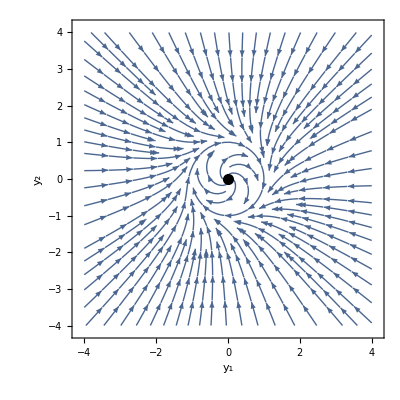

```mathematica
Module[{y1p,y2p},
y1p=y1+y2-y1 (y1^2+y2^2);
y2p=-y1+y2-y2 (y1^2+y2^2);
StreamPlot[{y1p,y2p},{y1,-4,4},{y2,-4,4},FrameLabel->{Subscript[y, 1],Subscript[y, 2]},Epilog->{PointSize[0.02],Point[{0,0}]}]]
```

By multiplying y_1 and y_2 to the two equations and adding them, we obtain

```mathematica
{Subscript[ẏ, 1]==Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 1](Subscript[y, 1]^2+Subscript[y, 2]^2),Subscript[ẏ, 2]==-Subscript[y, 1]+Subscript[y, 2]-Subscript[y, 2](Subscript[y, 1]^2+Subscript[y, 2]^2)}
SCMAF[%,SCMultEq,{{At[1],Subscript[y, 1]},{At[2],Subscript[y, 2]}},$,
SCAddEqs,All,Factor->At[2],
SCDerivSimp,{At[1],OverDot->t,Post->Simplify,DerivDot->Total},
RA,{All,Subscript[y, 1]^2+Subscript[y, 2]^2==z},,
SCDSolve,{All,z,t,ReplConst->Log[c],Post->SCDivDenom->ⅇ^(2 t)}]
```

{(ẏ)_1==y_1+y_2-y_1 (y_1^2+y_2^2),(ẏ)_2==-y_1+y_2-y_2 (y_1^2+y_2^2)}

{y_1 (ẏ)_1==y_1^2+y_1 y_2-y_1^2 (y_1^2+y_2^2),y_2 (ẏ)_2==-y_1 y_2+y_2^2-y_2^2 (y_1^2+y_2^2)}

where z=y_1^2+y_2^2. As t→+∞, z→1.

### Conversion of an nth-Order ODE to a System

Introductory video: Mass on a spring. The equation of motion is

```mathematica
v=Video["F:\\Office_Computer_From2021Jan\\Education\\2023\\Spring\\MathemaicaSymbolicComputing\\Lectures\\ToSetOfODEs_HamiltonMathod.mp4"]
```

Example: Mass on a spring. The equation of motion is

```mathematica
m y''+c y'+k y==0
SCMAF[%,SCDivide,{At[1],m},
SCEqMove,{All,y''}]
```

k y+c y'+m y''==0

(k y)/m+(c y')/m+y''==0

y''==-(k y)/m-(c y')/m

With y_1=y and y_2=y', we have

```mathematica
{Subscript[y, 1]'==Subscript[y, 2],y''==-(k y)/m-(c y')/m}
SCMAF[%,RA,{At[2],y==Subscript[y, 1]},
SCTransFunc,{At[2],Subscript[y, 1]'==Subscript[y, 2]},
SCEqsMatForm,{All,{Subscript[y, 1],Subscript[y, 2]}}]
```

{y'_1==y_2,y''==-(k y)/m-(c y')/m}

{y'_1==y_2,y'_2==-(k y_1)/m-(c y_2)/m}

(y'_1
y'_2)==(0 | 1
-k/m | -c/m)·(y_1
y_2)

The eigenvalues and eigenvectors

```mathematica
Eigensystem[({{0, 1}, {-k/m, -c/m}})]
```

{{(-c-√(c^2-4 k m))/(2 m),(-c+√(c^2-4 k m))/(2 m)},{{-(c-√(c^2-4 k m))/(2 k),1},{-(c+√(c^2-4 k m))/(2 k),1}}}

For m=1, c=2, and k=0.75, we have

```mathematica
{Subscript[λ, 1]==(-c-√(c^2-4 k m))/(2 m),Subscript[λ, 2]==(-c+√(c^2-4 k m))/(2 m),(x⃗)^1=={-(c-√(c^2-4 k m))/(2 k),1},(x⃗)^2=={-(c+√(c^2-4 k m))/(2 k),1}}
SCMAF[%,RA,{All,{m==1,c==2,k==0.75}},Post->Rationalize]
```

{λ_1==(-c-√(c^2-4 k m))/(2 m),λ_2==(-c+√(c^2-4 k m))/(2 m),(x⃗)^1=={-(c-√(c^2-4 k m))/(2 k),1},(x⃗)^2=={-(c+√(c^2-4 k m))/(2 k),1}}

{λ_1==-3/2,λ_2==-1/2,(x⃗)^1=={-2/3,1},(x⃗)^2=={-2,1}}

and the general solution is

```mathematica
{Subscript[y, 1][t],Subscript[y, 2][t]}==Subscript[c, 1] ⅇ^(Subscript[λ, 1] t)(x⃗)^1+Subscript[c, 2] ⅇ^(Subscript[λ, 2] t)(x⃗)^2
SCMAF[%,RA,{At[2],{Subscript[λ, 1]==-3/2,Subscript[λ, 2]==-1/2,(x⃗)^1=={-2/3,1},(x⃗)^2=={-2,1}}},PostAll->Thread]
```

{y_1[t],y_2[t]}==ⅇ^(t λ_1) (x⃗)^1 c_1+ⅇ^(t λ_2) (x⃗)^2 c_2

{y_1[t]==-2/3 ⅇ^(-3 t/2) c_1-2 ⅇ^(-t/2) c_2,y_2[t]==ⅇ^(-3 t/2) c_1+ⅇ^(-t/2) c_2}

```mathematica
SCCollectPoly[3 a x y+b x^2==2 x^2+c,{x,y},MatrixForm->True]
```

{0,b,3 a}·(1
x^2
x y)=={c,2,0}·(1
x^2
x y)

```mathematica
SCCollect[A ⅇ^(ⅈ k z+ⅈ Subscript[ϕ, 1])+C ⅇ^(ⅈ k z+ⅈ Subscript[ϕ, 1])+B ⅇ^(-ⅈ k z+ⅈ Subscript[ϕ, 2])+D,{ⅇ^(ⅈ k z),ⅇ^(-ⅈ k z)},MatrixForm->True]
```

{D,B ⅇ^(ⅈ ϕ_2),A ⅇ^(ⅈ ϕ_1)+C ⅇ^(ⅈ ϕ_1)}·(1
ⅇ^(-ⅈ k z)
ⅇ^(ⅈ k z))

```mathematica
SCDSolve[y'[x]+y[x]==0,y[x],x]
```

y[x]==ⅇ^-x C_1

```mathematica
SCDSolve[(2+x^2)y''-x y'[x]+4 y[x]==0,y[x],x]
```

y[x]==(2+x^2)^(3/4) C_1 LegendreP[1/2 ⅈ (ⅈ+2 √3),3/2,(ⅈ x)/(√2)]+(2+x^2)^(3/4) C_2 LegendreQ[1/2 ⅈ (ⅈ+2 √3),3/2,(ⅈ x)/(√2)]

### How to solve a differential equation and verify the solution.

```mathematica
SCMAF[{y'[x]-y[x]==x,y[0]==1},SCDSolve,{All,y[x],x}]
```

y[x]==-1+2 ⅇ^x-x

```mathematica
SCMAF[y'[x]-y[x]==x,SCDerivExpand,All,RA,{All,{y[x]==-1+2 ⅇ^x-x}},Post -> SCEvalDeriv]
```

ⅆy[x]/ⅆx-y[x]==x

True

### Series solution

### Solve y''+x^2 y=x^3.

Try the kernel function DSolve. The result is rather long.

```mathematica
y''+x^2 y==x^3
SCMAF[%,SCDSolve,{All,y,x}]
```

x^2 y+y''==x^3

y==C_2 ParabolicCylinderD[-1/2,(-1+ⅈ) x]+C_1 ParabolicCylinderD[-1/2,(1+ⅈ) x]+ParabolicCylinderD[-1/2,(1+ⅈ) x] ∫_1^x (-(ⅈ K[1]^2)/(2 ParabolicCylinderD[-1/2,(1+ⅈ) K[1]])-((1/4+ⅈ/4) K[1] (-ⅈ ParabolicCylinderD[-1/2,(1+ⅈ) K[1]] ParabolicCylinderD[1/2,(-1+ⅈ) K[1]]+ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[1/2,(1+ⅈ) K[1]]))/(ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[-1/2,(1+ⅈ) K[1]]^2)-(-ⅈ ParabolicCylinderD[-1/2,(1+ⅈ) K[1]] ParabolicCylinderD[1/2,(-1+ⅈ) K[1]]+ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[1/2,(1+ⅈ) K[1]])^2/(4 ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]]^2 ParabolicCylinderD[-1/2,(1+ⅈ) K[1]]^3)+(-ⅈ ParabolicCylinderD[-1/2,(1+ⅈ) K[1]]^3 ParabolicCylinderD[1/2,(-1+ⅈ) K[1]]^3+3 ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[-1/2,(1+ⅈ) K[1]]^2 ParabolicCylinderD[1/2,(-1+ⅈ) K[1]]^2 ParabolicCylinderD[1/2,(1+ⅈ) K[1]]+3 ⅈ ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]]^2 ParabolicCylinderD[-1/2,(1+ⅈ) K[1]] ParabolicCylinderD[1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[1/2,(1+ⅈ) K[1]]^2-ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]]^3 ParabolicCylinderD[1/2,(1+ⅈ) K[1]]^3)/(4 ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]]^2 ParabolicCylinderD[-1/2,(1+ⅈ) K[1]]^3 ((1+ⅈ) K[1] ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[-1/2,(1+ⅈ) K[1]]+ⅈ ParabolicCylinderD[-1/2,(1+ⅈ) K[1]] ParabolicCylinderD[1/2,(-1+ⅈ) K[1]]-ParabolicCylinderD[-1/2,(-1+ⅈ) K[1]] ParabolicCylinderD[1/2,(1+ⅈ) K[1]])))ⅆK[1]+ParabolicCylinderD[-1/2,(-1+ⅈ) x] ∫_1^x ((ⅈ K[2]^2)/(2 ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]])-(ParabolicCylinderD[-1/2,(1+ⅈ) K[2]] ParabolicCylinderD[1/2,(-1+ⅈ) K[2]]+ⅈ ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]] ParabolicCylinderD[1/2,(1+ⅈ) K[2]])^2/(4 ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]]^3 ParabolicCylinderD[-1/2,(1+ⅈ) K[2]]^2)+((1/4+ⅈ/4) K[2] (-ⅈ ParabolicCylinderD[-1/2,(1+ⅈ) K[2]] ParabolicCylinderD[1/2,(-1+ⅈ) K[2]]+ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]] ParabolicCylinderD[1/2,(1+ⅈ) K[2]]))/(ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]]^2 ParabolicCylinderD[-1/2,(1+ⅈ) K[2]])+(ⅈ (ParabolicCylinderD[-1/2,(1+ⅈ) K[2]]^3 ParabolicCylinderD[1/2,(-1+ⅈ) K[2]]^3+3 ⅈ ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]] ParabolicCylinderD[-1/2,(1+ⅈ) K[2]]^2 ParabolicCylinderD[1/2,(-1+ⅈ) K[2]]^2 ParabolicCylinderD[1/2,(1+ⅈ) K[2]]-3 ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]]^2 ParabolicCylinderD[-1/2,(1+ⅈ) K[2]] ParabolicCylinderD[1/2,(-1+ⅈ) K[2]] ParabolicCylinderD[1/2,(1+ⅈ) K[2]]^2-ⅈ ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]]^3 ParabolicCylinderD[1/2,(1+ⅈ) K[2]]^3))/(4 ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]]^3 ParabolicCylinderD[-1/2,(1+ⅈ) K[2]]^2 ((1+ⅈ) K[2] ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]] ParabolicCylinderD[-1/2,(1+ⅈ) K[2]]+ⅈ ParabolicCylinderD[-1/2,(1+ⅈ) K[2]] ParabolicCylinderD[1/2,(-1+ⅈ) K[2]]-ParabolicCylinderD[-1/2,(-1+ⅈ) K[2]] ParabolicCylinderD[1/2,(1+ⅈ) K[2]])))ⅆK[2]

Let us solve the homogeneous equation using the Frobenius series given by

(1)

y=∑_(n=0)^∞ a_n x^(n+λ),    a_0!=0,

where λ is a parameter to be determined. Substitution of Eq. (1) into the homogeneous equation gives

(2)

```mathematica
y''+x^2 y==0
SCMAF[%,RA,{All,y==∑_(n=0)^∞ Subscript[a, n] x^(n+λ)},Post->{SCInSum,SCEvalDeriv->Prime->x},
SCSumShiftVar,{∑_(n=0)^∞ x^(s_+n+λ) _,{n,-s}},
SCSumChangeLimits,{At[1],{n,2,∞}},SCMergeSums->Post->SCFactor->x^(n+λ)]
```

x^2 y+y''==0

∑_(n=2)^∞ x^(n+λ) a_(-2+n)+∑_(n=-2)^∞ x^(n+λ) (1+n+λ) (2+n+λ) a_(2+n)==0

∑_(n=2)^∞ x^(n+λ) (a_(-2+n)+(1+n+λ) (2+n+λ) a_(2+n))+x^(-2+λ) (-1+λ) λ a_0+x^(-1+λ) λ (1+λ) a_1+x^λ (1+λ) (2+λ) a_2+x^(1+λ) (2+λ) (3+λ) a_3==0

From vanishing of the two terms x^(λ-2) and x^(λ-1), the indicial equations are

(3)

λ (λ-1) =0,    λ (λ+1)=0.

Since both equations of Eq. (3) must be satisfied, the only solution is λ=0. In addition, for the two terms x^λ and x^(λ+1) to vanish, we require

(4)

a_2=0,    a_3=0.

a_0 and a_1 are the two free parameters.

The recursion relation of the coefficients a_n and the solution are

(5)

```mathematica
Subscript[a, -2+n]+(1+n+λ) (2+n+λ) Subscript[a, 2+n]==0/.λ->0
SCMAF[%,SCRSolve,{All,{Subscript[a, 2]==0,Subscript[a, 3]==0},Subscript[a, n],{n,{0,1}},Post->Collect->{{Subscript[a, 0],Subscript[a, 1]},Simplify}}]
```

a_(-2+n)+(1+n) (2+n) a_(2+n)==0

a_n==((-1)^(n/4) 2^(-2-n) a_0 (1+(-1)^n+2 Cos[(n π)/2])Γ[3/4])/(Γ[1+n/4] Γ[(3+n)/4])+((-1)^((3+n)/4) 2^(-1-n) a_1 (-1+(-1)^n-2 Sin[(n π)/2])Γ[5/4])/(Γ[1+n/4] Γ[(3+n)/4])

Listing of the terms a_2,a_3,…,a_9 in terms of a_0 and a_1

(6)

```mathematica
Table[Subscript[a, n]==((-1)^(n/4) 2^(-2-n) Subscript[a, 0] (1+(-1)^n+2 Cos[(n π)/2])Γ[3/4])/(Γ[1+n/4] Γ[(3+n)/4])+((-1)^((3+n)/4) 2^(-1-n) Subscript[a, 1] (-1+(-1)^n-2 Sin[(n π)/2])Γ[5/4])/(Γ[1+n/4] Γ[(3+n)/4]),{n,2,9}]
```

{a_2==0,a_3==0,a_4==-(a_0 Γ[3/4])/(16 Γ[7/4]),a_5==-(a_1 Γ[5/4])/(16 Γ[9/4]),a_6==0,a_7==0,a_8==(a_0 Γ[3/4])/(512 Γ[11/4]),a_9==(a_1 Γ[5/4])/(512 Γ[13/4])}

The general solution for a_(4n), a_(4n+1), a_(4n+2), a_(4n+3) (n=0,1,2,…)

(7)

```mathematica
Subscript[a, n]==((-1)^(n/4) 2^(-2-n) Subscript[a, 0] (1+(-1)^n+2 Cos[(n π)/2])Γ[3/4])/(Γ[1+n/4] Γ[(3+n)/4])+((-1)^((3+n)/4) 2^(-1-n) Subscript[a, 1] (-1+(-1)^n-2 Sin[(n π)/2])Γ[5/4])/(Γ[1+n/4] Γ[(3+n)/4])
SCMAF[%,RA,{All,{{n==4n},{n==4n+1},{n==4n+2},{n==4n+3}}},Post->{Simplify,RA->{Cos[2n π]->1,Sin[2n π]->0},SCExpandArg->Cos|Sin|Gamma,SCSimpToOne},
SCToFactorial,Γ[1+n]]
```

a_n==((-1)^(n/4) 2^(-2-n) a_0 (1+(-1)^n+2 Cos[(n π)/2])Γ[3/4])/(Γ[1+n/4] Γ[(3+n)/4])+((-1)^((3+n)/4) 2^(-1-n) a_1 (-1+(-1)^n-2 Sin[(n π)/2])Γ[5/4])/(Γ[1+n/4] Γ[(3+n)/4])

{a_(4 n)==((-1/16)^n a_0 Γ[3/4])/(Γ[1+n] Γ[3/4+n]),a_(1+4 n)==((-1/16)^n a_1 Γ[5/4])/(Γ[1+n] Γ[5/4+n]),a_(2+4 n)==0,a_(3+4 n)==0}

{a_(4 n)==((-1/16)^n a_0 Γ[3/4])/(n! Γ[3/4+n]),a_(1+4 n)==((-1/16)^n a_1 Γ[5/4])/(n! Γ[5/4+n]),a_(2+4 n)==0,a_(3+4 n)==0}

Substituting Eq. (7) into Eq. (1), we obtain the homogeneous solution:

(8)

```mathematica
Subscript[y, h]==∑_(n=0)^∞ Subscript[a, n] x^(n+λ)/.λ->0
SCMAF[%,SCSumChangeInterval,{At[2],{n,{0,∞,n==4n},{0,∞,n==4n+1}}},
RA,{At[2],{Subscript[a, 4 n]==((-1/16)^n Subscript[a, 0] Γ[3/4])/(n! Γ[3/4+n]),Subscript[a, 1+4 n]==((-1/16)^n Subscript[a, 1] Γ[5/4])/(n! Γ[5/4+n])}},SCFactorSum->Exponent->False]
```

y_h==∑_(n=0)^∞ x^n a_n

y_h==∑_(n=0)^∞ x^(4 n) a_(4 n)+∑_(n=0)^∞ x^(1+4 n) a_(1+4 n)

y_h==a_0 Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+a_1 Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n])

Evaluating the sums on the right-hand side gives the closed-form solution in terms of the Bessel functions J_(±1/4).

(9)

```mathematica
Subscript[y, h]==Subscript[a, 0] Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+Subscript[a, 1] Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n])
SCMAF[%,SCEvalSum,At[2],Post->{SCFuncShort,PowerExpand},
RA,{At[2],{(Subscript[a, 0] Γ[3/4])/(√2)->A,(4 √2 Subscript[a, 1] Γ[5/4]^2)/Γ[1/4]->B}},SCFactor->√x]
```

y_h==a_0 Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+a_1 Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n])

y_h==(√x a_0 Γ[3/4])/(√2) J_(-1/4)[x^2/2]+(4 √2 √x a_1 J_(1/4)[x^2/2]Γ[5/4]^2)/Γ[1/4]

y_h==√x (A J_(-1/4)[x^2/2]+B J_(1/4)[x^2/2])

where A and B are arbitrary constants.

For the particular solution, let us assume a polynomial in the form

(10)

y_p=b_0+b_1 x.

Subsituting Eq. (10) into Eq. (1), we can determine the coefficients b_0 and b_1:

(11)

```mathematica
y''+x^2 y==x^3
SCMAF[%,RA,{At[1],y==Subscript[b, 0]+Subscript[b, 1] x},SCEvalDeriv->Prime->x,Post->Expand,
SCCollect,{All,x,Coefficient->True},Post->Thread]
```

x^2 y+y''==x^3

x^2 b_0+x^3 b_1==x^3

{b_0==0,b_1==1}

and hence,

(12)

```mathematica
Subscript[y, p]==Subscript[b, 0]+Subscript[b, 1] x/.{Subscript[b, 0]->0,Subscript[b, 1]->1}
```

y_p==x

The full solution is y=y_h+y_p.

(13)

```mathematica
y==Subscript[y, h]+Subscript[y, p]
SCMAF[%,RA,{At[2],{Subscript[y, h]==Subscript[a, 0] Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+Subscript[a, 1] Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n]),Subscript[y, p]==x}}]
```

y==y_h+y_p

y==x+a_0 Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+a_1 Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n])

In closed form,

(14)

```mathematica
y==Subscript[y, h]+Subscript[y, p]
SCMAF[%,RA,{At[2],{Subscript[y, h]==√x (A Subscript[J, -1/4][x^2/2]+B Subscript[J, 1/4][x^2/2]),Subscript[y, p]==x}}]
```

y==y_h+y_p

y==x+√x (A J_(-1/4)[x^2/2]+B J_(1/4)[x^2/2])

Verify.

(15)

```mathematica
y''+x^2 y==x^3
SCMAF[%,RA,{At[1],y==x+Subscript[a, 0] Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+Subscript[a, 1] Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n])},Post->{SCSimpGamma,SCSimpFactorial,Expand,SCEvalDeriv->Prime->x},
SCSumShiftVar,{∑_(n=0)^∞ 1/((-1+n)!)_,{n,1}},Post->SCExpandExp,
SCSumChangeLimits,{At[1],{n,0,∞}},SCMergeSums->Post->Simplify]
```

x^2 y+y''==x^3

x^3+x^2 a_0 Γ[3/4]∑_(n=0)^∞ ((-1/16)^n x^(4 n))/(n! Γ[3/4+n])+a_0 Γ[3/4]∑_(n=-1)^∞ ((-1)^(1+n) 4^(-2 n) x^(2+4 n))/(n! Γ[3/4+n])+x^2 a_1 Γ[5/4]∑_(n=0)^∞ ((-1/16)^n x^(1+4 n))/(n! Γ[5/4+n])+a_1 Γ[5/4]∑_(n=-1)^∞ ((-1)^(1+n) 4^(-2 n) x^(3+4 n))/(n! Γ[5/4+n])==x^3

True

In closed form,

(16)

```mathematica
y''+x^2 y==x^3
SCMAF[%,RA,{At[1],y==x+√x (A Subscript[J, -1/4][x^2/2]+B Subscript[J, 1/4][x^2/2])},Post->{FullSimplify,SCEvalDeriv->Prime->x,SCFuncNormal}]
```

x^2 y+y''==x^3

True